## COME FAREI IO

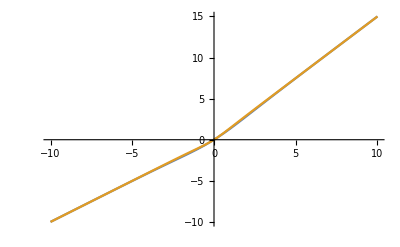

```mathematica
(* setup *)
ftrue[x_]:=x(1+0.5 (1+E^(-x))^(-1)); (* modello "vero" dal quale si generano i dati *)
atrue=1;
btrue=0.5;
fmod[x_,a_,b_]:=x(1+b (1+E^(-a x))^(-1));
loss[x_,y_,a_,b_]:=(y -fmod[x,a,b])^2; (* questa è solo la parte quadratica, senza somma o normalizzazione*)
gradloss[x_,y_,a_,b_]:={D[(y -fmod[x,a,b])^2,a],D[(y -fmod[x,a,b])^2,b]} ;
Plot[{ftrue[x],fmod[x,2,0.5]},{x,-10,10}]
```

```mathematica
(* generate a sample from ftrue*)
```

```mathematica
nn=50;
ll=100;
ntot=nn ll; (*number of datapoints*)
xs = Table[xi-Floor[nn/2],{ xi,1,nn}];
fi=Table[N[ftrue[x/.(x->xs[[i]])]],{i,1,Length[xs]}];
eps=5;
epss = RandomReal[{-eps,eps},ll*Length[fi]];
data=Table[{xs[[i]],Table[fi[[i]]+epss[[i+j]],{j,0,ll-1}]},{i,1,Length[fi]}];
```

```mathematica
(******genero dati per l'errore di generalizzazione************)
nnp= Floor[N[nn/5]];
Print[nnp];
llp = Floor[N[ll]];
Print[llp];
ntotp=nnp llp; (*number of datapoints*)
xsp = Table[xi-Floor[nnp/2],{ xi,1,nnp}];
fip=Table[N[ftrue[x/.(x->xsp[[i]])]],{i,1,Length[xsp]}];
epssp = RandomReal[{-eps,eps},llp*Length[fip]];
datap=Table[{xsp[[i]],Table[fip[[i]]+epssp[[i+j]],{j,0,llp-1}]},{i,1,Length[fip]}];
lossp[a_,b_]:=1/ntotp Sum[ Sum[(datap[[i,2]][[j]]-fmod[datap[[i,1]],a,b])^2,{j,1,llp}],{i,1,nnp}];(*loss function per il validation set; DEBUG: normalizzazione *)
(*********************************************************)
```

10

100

-Graphics3D-

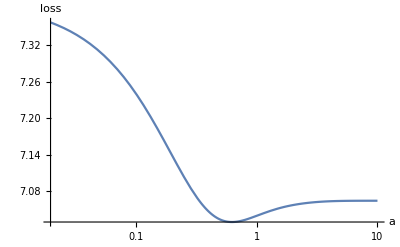

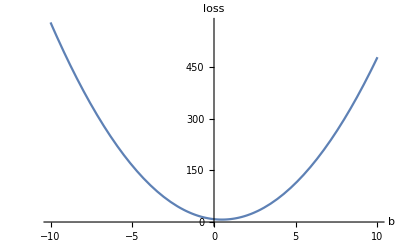

```mathematica
l=10;
Plot3D[lossp[a,b],{a,-l,l},{b,-1,1}, AxesLabel->{"a","b"}]
LogLinearPlot[lossp[a,0.5],{a,-l,l}, AxesLabel->{"a","loss"}]
Plot[lossp[1,b],{b,-l,l}, AxesLabel->{"b","loss"}]
```

```mathematica
(* IPERPARAMETRI DEL SGD *)
maxite =10000;
eta =0.0005;
bsize =25;

(* costruisco il vettore dei parametri che ottimizzo, tengo tutti le iterazioni per la visualizzazione *)
v = Table[{0,0},{ite,1,maxite}];
lossvalues=Table[0,{ite,1,maxite}]; (* per visualizzazione *)
totlossvalues=Table[0,{ite,1,maxite}]; (* sarebbe la loss usata nel GD *)
(*guess iniziale; lo puoi anche lasciare fisso con un certo seed per debuggare*)
a0 =RandomReal[];
b0=RandomReal[];
v[[1]]={a0,b0};
```

```mathematica
(*  SGD loop **************************************************************)
(* nota: faccio il caso semplice del ciclo for, si può sostituire con un while per controllare se sta raggiungendo la convergenza *)
For[ite=2,ite<=maxite, ite++,
If[Mod[ite,10000]==0, Print["ite: ",ite, "/ ", maxite]];
ai = v[[ite-1]][[1]];
bi= v[[ite-1]][[2]];

(* sceglie il nuovo minibatch *)
xidxs =RandomInteger[{1,nn},bsize];
yidxs=RandomInteger[{1,ll},bsize]; (* nota che si fa così solo per il modo in cui ho costruito i dati, in generale non devi scegliere x e y in maniera indipendente!*)
xis =Table[ data[[xidxs[[bidx]],1]], {bidx,1,bsize}];
yis = Table[data[[xidxs[[bidx]],2]][[yidxs[[bidx]] ]],{bidx,1,bsize}];


(* solo per visualizzazione; calcolo la loss function per il minibatch *)  
lossvalues[[ite]]= 1/bsize 
 Sum[
N[loss[xis[[bidx]],yis[[bidx]], ai,bi]],
{bidx,1,bsize}
];

(* calcola il gradiente medio della loss rispetto ai parametri *) 
gradlossvector= 1/bsize 
 Sum[
(gradloss[xis[[bidx]],yis[[bidx]], z1,z2]/.{z1->ai,z2->bi}),
{bidx,1,bsize}
];

(* calcola l'incremento *)
dai =eta gradlossvector[[1]];
dbi =eta gradlossvector[[2]];
v[[ite]]={ai-dai, bi-dbi}
]
(***********************************************************************)
```

ite: 10000/ 10000

```mathematica
(* time continuous SDE *)
(***************Discretizzo la SDE del paper e simulo le traiettorie**********)
timestep=0.0005;
maxtimes= 1001;
etasgd =eta;
bsizesgd =bsize;Table::iterb: "Iterator \!\(\*RowBox[{\"{\", RowBox[{\"ite\", \",\", \"1\", \",\", \"maxtimes\"}], \"}\"}]\) does not have appropriate bounds."
vc = Table[{0,0},{ite,1,maxtimes}];
vc[[1]]={a0,b0};

(*calcolo l'hessiano, lo valuto su tutto il set e nel punto di minimo nello spazio dei parametri(che conosco)*)
hessloss[x_,y_,a_,b_]:= {{D[D[(y -fmod[x,a,b])^2,a],a],D[D[(y -fmod[x,a,b])^2,a],b]},{D[D[(y -fmod[x,a,b])^2,b],a],D[D[(y -fmod[x,a,b])^2,b],b]}};
hesslossmin= Sum[Sum[hessloss[data[[i,1]],data[[i,2]][[j]],x,y]/.{x->atrue,y->btrue},{j,1,ll}],{i,1,nn}]
sqrthesslossmin=MatrixPower[ hesslossmin, 1/2]
Print[N[hesslossmin],"*"]
Print[Eigenvalues[hesslossmin],"*"]
Print[N[sqrthesslossmin]]
```

Table::iterb

{{159.732,78.7609},{78.7609,63000/((1+1/ⅇ^30)^2)+58870/((1+1/ⅇ^29)^2)+54880/((1+1/ⅇ^28)^2)+51030/((1+1/ⅇ^27)^2)+47320/((1+1/ⅇ^26)^2)+43750/((1+1/ⅇ^25)^2)+40320/((1+1/ⅇ^24)^2)+37030/((1+1/ⅇ^23)^2)+33880/((1+1/ⅇ^22)^2)+30870/((1+1/ⅇ^21)^2)+28000/((1+1/ⅇ^20)^2)+25270/((1+1/ⅇ^19)^2)+22680/((1+1/ⅇ^18)^2)+20230/((1+1/ⅇ^17)^2)+17920/((1+1/ⅇ^16)^2)+15750/((1+1/ⅇ^15)^2)+13720/((1+1/ⅇ^14)^2)+11830/((1+1/ⅇ^13)^2)+10080/((1+1/ⅇ^12)^2)+8470/((1+1/ⅇ^11)^2)+7000/((1+1/ⅇ^10)^2)+5670/((1+1/ⅇ^9)^2)+4480/((1+1/ⅇ^8)^2)+3430/((1+1/ⅇ^7)^2)+2520/((1+1/ⅇ^6)^2)+1750/((1+1/ⅇ^5)^2)+1120/((1+1/ⅇ^4)^2)+630/((1+1/ⅇ^3)^2)+280/((1+1/ⅇ^2)^2)+70/(1+1/ⅇ)^2+70/(1+ⅇ)^2+280/((1+ⅇ^2)^2)+630/((1+ⅇ^3)^2)+1120/((1+ⅇ^4)^2)+1750/((1+ⅇ^5)^2)+2520/((1+ⅇ^6)^2)+3430/((1+ⅇ^7)^2)+4480/((1+ⅇ^8)^2)+5670/((1+ⅇ^9)^2)+7000/((1+ⅇ^10)^2)+8470/((1+ⅇ^11)^2)+10080/((1+ⅇ^12)^2)+11830/((1+ⅇ^13)^2)+13720/((1+ⅇ^14)^2)+15750/((1+ⅇ^15)^2)+17920/((1+ⅇ^16)^2)+20230/((1+ⅇ^17)^2)+22680/((1+ⅇ^18)^2)+25270/((1+ⅇ^19)^2)+28000/((1+ⅇ^20)^2)+30870/((1+ⅇ^21)^2)+33880/((1+ⅇ^22)^2)+37030/((1+ⅇ^23)^2)+40320/((1+ⅇ^24)^2)+43750/((1+ⅇ^25)^2)+47320/((1+ⅇ^26)^2)+51030/((1+ⅇ^27)^2)+54880/((1+ⅇ^28)^2)+58870/((1+ⅇ^29)^2)}}

{{12.6382,0.0953478},{0.0953478,813.4}}

{{159.732,78.7609},{78.7609,661620.}}*

{661620.,159.723}*

{{12.6382,0.0953478},{0.0953478,813.4}}

```mathematica
(*calcolo la loss function su tutto il set di dati, in funzione dei parametri: DEBUG: mancava la normalizzazione *)
loss[a_,b_]:=1/ntot Sum[ Sum[(data[[i,2]][[j]]-fmod[data[[i,1]],a,b])^2,{j,1,ll}],{i,1,nn}];

(*calcolo il gradiente su tutto il set di dati DEBUG: mancava la normalizzazione *)
gradlosstot[a_,b_]:=1/ntot Sum[Sum[gradloss[data[[i,1]],data[[i,2]][[j]],x,y],{j,1,ll}],{i,1,nn}]/.{x->a,y->b}

(*calcolo la dinamica*)
For[ite=2,ite≤maxtimes, ite++,
Z={RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]};
Zscale= sqrthesslossmin.Z; 
ai = vc[[ite-1]][[1]];
bi= vc[[ite-1]][[2]];
vc[[ite]][[1]]= ai-gradlosstot[x,y][[1]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[1]]*Sqrt[timestep]/.{x->ai,y->bi};
vc[[ite]][[2]]= bi-gradlosstot[x,y][[2]]*timestep+Sqrt[(2*etasgd/bsizesgd)*loss[x,y]]*Zscale[[2]]*Sqrt[timestep]/.{x->ai,y->bi};
If[Mod[ite,1000]==0, Print[ite]/maxtimes," ",Print[vc[[ite]]]];
]
(*****************************************************************************)
```

General::munfl: 1/((9.01793×10^156)^2) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
(************Calcolo la dinamica del GD*******************************************)
maxite2=1000;
etagd = 0.0001
vgd = Table[{0,0},{ite,1,maxite2}];
vgd[[1]]={0.1,3};
For[ite=2,ite<=maxite2, ite++,
ai = vgd[[ite-1]][[1]];
bi= vgd[[ite-1]][[2]];

(* calcola l'incremento *)
dai =etagd gradlosstot[x,y][[1]]/.{x->ai,y->bi};
dbi =etagd gradlosstot[x,y][[2]]/.{x->ai,y->bi};
vgd[[ite]]={ai-dai, bi-dbi}
If[Mod[ite,100]==0, Print[ite]/maxite2," ",Print[vgd[[ite]]]]
]


(******************************************************************************)
```

0.0001

```mathematica
(* risultato: stima finale per a,b e confronto con quelli del modello vero *) 
Print["parametri stimati, SGD: ", v[[-1]]]
Print["parametri stimati, SDE: ", vc[[-1]]]
Print["parametri stimati, GD: ", vgd[[-1]]]
Print["a0, b0: ", a0," ",b0]
Print["atrue, btrue: ", atrue," ",btrue]
insamplesgd = loss[x,y]/.{x->v[[-1]][[1]],y->v[[-1]][[2]]};
insamplegd = loss[x,y]/.{x->vgd[[-1]][[1]],y->vgd[[-1]][[2]]};
insamplesde = loss[x,y]/.{x->vc[[-1]][[1]],y->vc[[-1]][[2]]};

outsamplesgd = lossp[x,y]/.{x->v[[-1]][[1]],y->v[[-1]][[2]]};
outsamplegd = lossp[x,y]/.{x->vgd[[-1]][[1]],y->vgd[[-1]][[2]]};
outsamplesde = lossp[x,y]/.{x->vc[[-1]][[1]],y->vc[[-1]][[2]]};

Print["In-sample error, SGD: ", insamplesgd," "]
Print["In-sample error, GD: ", insamplegd," "]
Print["In-sample error, SDE: ", insamplesde," "]

Print["Out-of-sample error, SGD: ", outsamplesgd," "]
Print["Out-of-sample error, GD: ", outsamplegd," "]
Print["Out-of-sample error, SDE: ", outsamplesde," "]

(* nei plot ricordati di mettere i nomi degli assi, le unità di misura se servono ecc. *)
Show[
ListLinePlot[Table[{ite,v[[ite]][[1]]},{ite,1,maxite}],
AxesOrigin->{0,0},
AxesLabel->{"iteration",""} ,PlotLegends->{"a"},PlotStyle->{Green}],
ListLinePlot[Table[{ite,v[[ite]][[2]]},{ite,1,maxite}],AxesOrigin->{0,0},
PlotLegends->{"b"},PlotStyle->{Blue}],PlotRange->All
]
ListLinePlot[Table[{ite,lossvalues[[ite]]},{ite,1,maxite}],PlotLegends->{"loss"},PlotStyle->{Red},
AxesLabel->{"iteration",""},
ScalingFunctions->{"Log","Log"},PlotRange->All]
ListPlot[Table[{ite,lossvalues[[ite]]},{ite,1,maxite}],PlotLegends->{"loss"},PlotStyle->{Red,Opacity[0.2]},
AxesLabel->{"iteration",""},PlotRange->All]
ListLinePlot[Table[{v[[ite]][[1]],v[[ite]][[2]]},{ite,1,maxite}],PlotLegends->{"SGD dynamics"},PlotStyle->{Red,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All]
ListLinePlot[Table[{vc[[ite]][[1]],vc[[ite]][[2]]},{ite,1,maxtimes}],PlotLegends->{"SDE dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All]
ListLinePlot[Table[{vgd[[ite]][[1]],vgd[[ite]][[2]]},{ite,1,maxtimes}],PlotLegends->{"GD dynamics"},PlotStyle->{Blue,Opacity[0.5]},
AxesLabel->{"a","b"},PlotRange->All]
```

Part::partd: Part specification v⟦-1⟧ is longer than depth of object.

parametri stimati, SGD: v⟦-1⟧

Part::partd: Part specification vc⟦-1⟧ is longer than depth of object.

parametri stimati, SDE: vc⟦-1⟧

Part::partd: Part specification vgd⟦-1⟧ is longer than depth of object.

parametri stimati, GD: vgd⟦-1⟧

a0, b0: a0 b0

atrue, btrue: 1 0.5

Part::partd: Part specification v⟦-1⟧ is longer than depth of object.

Part::partd: Part specification vgd⟦-1⟧ is longer than depth of object.

Part::partd: Part specification vc⟦-1⟧ is longer than depth of object.

Part::partd: Part specification v⟦-1⟧ is longer than depth of object.

Part::partd: Part specification vgd⟦-1⟧ is longer than depth of object.

Part::partd: Part specification vc⟦-1⟧ is longer than depth of object.

In-sample error, SGD: loss[v,-1]

In-sample error, GD: loss[vgd,-1]

In-sample error, SDE: loss[vc,-1]

Out-of-sample error, SGD: 1/1000(691.828+(-4.4453+1/(1+ⅇ^-v))^2+(-4.31113+1/(1+ⅇ^-v))^2+(-4.19885+1/(1+ⅇ^-v))^2+(-4.14361+1/(1+ⅇ^-v))^2+(-3.80855+1/(1+ⅇ^-v))^2+(-3.66276+1/(1+ⅇ^-v))^2+(-3.42632+1/(1+ⅇ^-v))^2+(-3.33508+1/(1+ⅇ^-v))^2+(-3.33079+1/(1+ⅇ^-v))^2+(-3.16011+1/(1+ⅇ^-v))^2+(-3.09452+1/(1+ⅇ^-v))^2+(-3.05882+1/(1+ⅇ^-v))^2+(-2.87089+1/(1+ⅇ^-v))^2+(-2.83945+1/(1+ⅇ^-v))^2+(-2.78423+1/(1+ⅇ^-v))^2+(-2.60234+1/(1+ⅇ^-v))^2+(-2.59621+1/(1+ⅇ^-v))^2+(-2.54223+1/(1+ⅇ^-v))^2+(-2.53999+1/(1+ⅇ^-v))^2+(-2.36478+1/(1+ⅇ^-v))^2+(-2.34418+1/(1+ⅇ^-v))^2+(-2.12068+1/(1+ⅇ^-v))^2+(-2.11601+1/(1+ⅇ^-v))^2+(-2.04716+1/(1+ⅇ^-v))^2+(-1.9451+1/(1+ⅇ^-v))^2+(-1.85873+1/(1+ⅇ^-v))^2+(-1.61668+1/(1+ⅇ^-v))^2+(-1.54995+1/(1+ⅇ^-v))^2+(-1.53908+1/(1+ⅇ^-v))^2+(-1.36017+1/(1+ⅇ^-v))^2+(-1.34323+1/(1+ⅇ^-v))^2+(-1.30296+1/(1+ⅇ^-v))^2+(-1.28649+1/(1+ⅇ^-v))^2+(-1.26636+1/(1+ⅇ^-v))^2+(-1.18697+1/(1+ⅇ^-v))^2+(-1.15899+1/(1+ⅇ^-v))^2+(-1.10306+1/(1+ⅇ^-v))^2+(-0.919833+1/(1+ⅇ^-v))^2+(-0.91886+1/(1+ⅇ^-v))^2+(-0.884793+1/(1+ⅇ^-v))^2+(-0.77997+1/(1+ⅇ^-v))^2+(-0.72852+1/(1+ⅇ^-v))^2+(-0.68674+1/(1+ⅇ^-v))^2+(-0.483712+1/(1+ⅇ^-v))^2+(-0.468945+1/(1+ⅇ^-v))^2+(-0.387756+1/(1+ⅇ^-v))^2+(-0.330495+1/(1+ⅇ^-v))^2+(-0.271019+1/(1+ⅇ^-v))^2+(-0.245975+1/(1+ⅇ^-v))^2+(-0.233382+1/(1+ⅇ^-v))^2+(-0.105642+1/(1+ⅇ^-v))^2+(-0.0224696+1/(1+ⅇ^-v))^2+(0.0454915+1/(1+ⅇ^-v))^2+(0.0530678+1/(1+ⅇ^-v))^2+(0.104519+1/(1+ⅇ^-v))^2+(0.203459+1/(1+ⅇ^-v))^2+(0.460207+1/(1+ⅇ^-v))^2+(0.533064+1/(1+ⅇ^-v))^2+(0.584018+1/(1+ⅇ^-v))^2+(0.731105+1/(1+ⅇ^-v))^2+(0.732112+1/(1+ⅇ^-v))^2+(0.951314+1/(1+ⅇ^-v))^2+(1.02504+1/(1+ⅇ^-v))^2+(1.05532+1/(1+ⅇ^-v))^2+(1.17646+1/(1+ⅇ^-v))^2+(1.25285+1/(1+ⅇ^-v))^2+(1.40964+1/(1+ⅇ^-v))^2+(1.44312+1/(1+ⅇ^-v))^2+(1.49446+1/(1+ⅇ^-v))^2+(1.52326+1/(1+ⅇ^-v))^2+(2.39672+1/(1+ⅇ^-v))^2+(2.4755+1/(1+ⅇ^-v))^2+(2.47745+1/(1+ⅇ^-v))^2+(2.52624+1/(1+ⅇ^-v))^2+(2.52736+1/(1+ⅇ^-v))^2+(2.62594+1/(1+ⅇ^-v))^2+(2.63499+1/(1+ⅇ^-v))^2+(2.67202+1/(1+ⅇ^-v))^2+(2.69897+1/(1+ⅇ^-v))^2+(2.77688+1/(1+ⅇ^-v))^2+(2.81196+1/(1+ⅇ^-v))^2+(3.24942+1/(1+ⅇ^-v))^2+(3.3229+1/(1+ⅇ^-v))^2+(3.61057+1/(1+ⅇ^-v))^2+(3.6592+1/(1+ⅇ^-v))^2+(3.84217+1/(1+ⅇ^-v))^2+(3.84579+1/(1+ⅇ^-v))^2+(3.90458+1/(1+ⅇ^-v))^2+(4.02532+1/(1+ⅇ^-v))^2+(4.10675+1/(1+ⅇ^-v))^2+(4.18269+1/(1+ⅇ^-v))^2+(4.33215+1/(1+ⅇ^-v))^2+(4.38737+1/(1+ⅇ^-v))^2+(4.47683+1/(1+ⅇ^-v))^2+(4.54772+1/(1+ⅇ^-v))^2+(4.72976+1/(1+ⅇ^-v))^2+(4.8632+1/(1+ⅇ^-v))^2+(5.25003+1/(1+ⅇ^-v))^2+(5.26486+1/(1+ⅇ^-v))^2+(5.3576+1/(1+ⅇ^-v))^2+(-4.9453-1/(1+ⅇ^v))^2+(-4.81113-1/(1+ⅇ^v))^2+(-4.69885-1/(1+ⅇ^v))^2+(-4.64361-1/(1+ⅇ^v))^2+(-4.30855-1/(1+ⅇ^v))^2+(-4.16276-1/(1+ⅇ^v))^2+(-3.92632-1/(1+ⅇ^v))^2+(-3.83508-1/(1+ⅇ^v))^2+(-3.83079-1/(1+ⅇ^v))^2+(-3.66011-1/(1+ⅇ^v))^2+(-3.59452-1/(1+ⅇ^v))^2+(-3.55882-1/(1+ⅇ^v))^2+(-3.37089-1/(1+ⅇ^v))^2+(-3.33945-1/(1+ⅇ^v))^2+(-3.28423-1/(1+ⅇ^v))^2+(-3.10234-1/(1+ⅇ^v))^2+(-3.09621-1/(1+ⅇ^v))^2+(-3.04223-1/(1+ⅇ^v))^2+(-3.03999-1/(1+ⅇ^v))^2+(-2.86478-1/(1+ⅇ^v))^2+(-2.84418-1/(1+ⅇ^v))^2+(-2.62068-1/(1+ⅇ^v))^2+(-2.61601-1/(1+ⅇ^v))^2+(-2.54716-1/(1+ⅇ^v))^2+(-2.35873-1/(1+ⅇ^v))^2+(-2.11668-1/(1+ⅇ^v))^2+(-2.04995-1/(1+ⅇ^v))^2+(-2.03908-1/(1+ⅇ^v))^2+(-1.86017-1/(1+ⅇ^v))^2+(-1.84323-1/(1+ⅇ^v))^2+(-1.80296-1/(1+ⅇ^v))^2+(-1.78649-1/(1+ⅇ^v))^2+(-1.76636-1/(1+ⅇ^v))^2+(-1.68697-1/(1+ⅇ^v))^2+(-1.65899-1/(1+ⅇ^v))^2+(-1.60306-1/(1+ⅇ^v))^2+(-1.41983-1/(1+ⅇ^v))^2+(-1.41886-1/(1+ⅇ^v))^2+(-1.38479-1/(1+ⅇ^v))^2+(-1.27997-1/(1+ⅇ^v))^2+(-1.22852-1/(1+ⅇ^v))^2+(-1.18674-1/(1+ⅇ^v))^2+(-0.983712-1/(1+ⅇ^v))^2+(-0.968945-1/(1+ⅇ^v))^2+(-0.887756-1/(1+ⅇ^v))^2+(-0.830495-1/(1+ⅇ^v))^2+(-0.771019-1/(1+ⅇ^v))^2+(-0.745975-1/(1+ⅇ^v))^2+(-0.733382-1/(1+ⅇ^v))^2+(-0.605642-1/(1+ⅇ^v))^2+(-0.52247-1/(1+ⅇ^v))^2+(-0.454508-1/(1+ⅇ^v))^2+(-0.446932-1/(1+ⅇ^v))^2+(-0.395481-1/(1+ⅇ^v))^2+(-0.296541-1/(1+ⅇ^v))^2+(-0.039793-1/(1+ⅇ^v))^2+(0.0330639-1/(1+ⅇ^v))^2+(0.0840183-1/(1+ⅇ^v))^2+(0.231105-1/(1+ⅇ^v))^2+(0.232112-1/(1+ⅇ^v))^2+(0.451314-1/(1+ⅇ^v))^2+(0.525041-1/(1+ⅇ^v))^2+(0.555319-1/(1+ⅇ^v))^2+(0.676456-1/(1+ⅇ^v))^2+(0.752849-1/(1+ⅇ^v))^2+(0.909638-1/(1+ⅇ^v))^2+(0.943116-1/(1+ⅇ^v))^2+(0.976653-1/(1+ⅇ^v))^2+(0.994457-1/(1+ⅇ^v))^2+(1.02326-1/(1+ⅇ^v))^2+(1.89672-1/(1+ⅇ^v))^2+(1.9755-1/(1+ⅇ^v))^2+(1.97745-1/(1+ⅇ^v))^2+(2.02624-1/(1+ⅇ^v))^2+(2.02736-1/(1+ⅇ^v))^2+(2.12594-1/(1+ⅇ^v))^2+(2.13499-1/(1+ⅇ^v))^2+(2.17202-1/(1+ⅇ^v))^2+(2.19897-1/(1+ⅇ^v))^2+(2.27688-1/(1+ⅇ^v))^2+(2.31196-1/(1+ⅇ^v))^2+(2.74942-1/(1+ⅇ^v))^2+(2.76127-1/(1+ⅇ^v))^2+(2.8229-1/(1+ⅇ^v))^2+(3.11057-1/(1+ⅇ^v))^2+(3.1592-1/(1+ⅇ^v))^2+(3.34217-1/(1+ⅇ^v))^2+(3.34579-1/(1+ⅇ^v))^2+(3.40458-1/(1+ⅇ^v))^2+(3.52532-1/(1+ⅇ^v))^2+(3.60675-1/(1+ⅇ^v))^2+(3.68269-1/(1+ⅇ^v))^2+(3.83215-1/(1+ⅇ^v))^2+(3.88737-1/(1+ⅇ^v))^2+(3.97683-1/(1+ⅇ^v))^2+(4.04772-1/(1+ⅇ^v))^2+(4.3632-1/(1+ⅇ^v))^2+(4.75003-1/(1+ⅇ^v))^2+(4.76486-1/(1+ⅇ^v))^2+(4.8576-1/(1+ⅇ^v))^2+(2.67244-5 (1-1/(1+ⅇ^(-5 v))))^2+(2.80661-5 (1-1/(1+ⅇ^(-5 v))))^2+(2.91888-5 (1-1/(1+ⅇ^(-5 v))))^2+(2.97413-5 (1-1/(1+ⅇ^(-5 v))))^2+(3.30919-5 (1-1/(1+ⅇ^(-5 v))))^2+(3.45498-5 (1-1/(1+ⅇ^(-5 v))))^2+(3.69142-5 (1-1/(1+ⅇ^(-5 v))))^2+(3.78265-5 (1-1/(1+ⅇ^(-5 v))))^2+(3.78695-5 (1-1/(1+ⅇ^(-5 v))))^2+(3.95763-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.02322-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.05892-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.27829-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.33351-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.5154-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.52153-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.57551-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.57775-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.75296-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.77356-5 (1-1/(1+ⅇ^(-5 v))))^2+(4.99706-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.00173-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.07058-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.17264-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.25901-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.50106-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.56779-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.57866-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.75757-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.77451-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.81478-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.83125-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.93076-5 (1-1/(1+ⅇ^(-5 v))))^2+(5.95875-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.01468-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.19791-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.19888-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.23295-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.33777-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.431-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.63403-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.64879-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.72998-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.78724-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.84672-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.87176-5 (1-1/(1+ⅇ^(-5 v))))^2+(6.88436-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.0121-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.09527-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.17081-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.22226-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.3212-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.57795-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.6461-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.6508-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.70176-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.72808-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.84884-5 (1-1/(1+ⅇ^(-5 v))))^2+(7.84985-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.06905-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.09804-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.14278-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.17306-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.29419-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.37059-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.52738-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.56085-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.6122-5 (1-1/(1+ⅇ^(-5 v))))^2+(8.641-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.51446-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.59324-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.59519-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.64398-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.6451-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.74368-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.75273-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.78976-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.81671-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.89462-5 (1-1/(1+ⅇ^(-5 v))))^2+(9.9297-5 (1-1/(1+ⅇ^(-5 v))))^2+(10.3672-5 (1-1/(1+ⅇ^(-5 v))))^2+(10.4406-5 (1-1/(1+ⅇ^(-5 v))))^2+(10.7283-5 (1-1/(1+ⅇ^(-5 v))))^2+(10.7769-5 (1-1/(1+ⅇ^(-5 v))))^2+(10.9599-5 (1-1/(1+ⅇ^(-5 v))))^2+(10.9635-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.0223-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.1431-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.2245-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.3004-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.4499-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.5051-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.5946-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.6175-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.6655-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.8475-5 (1-1/(1+ⅇ^(-5 v))))^2+(11.9809-5 (1-1/(1+ⅇ^(-5 v))))^2+(12.3678-5 (1-1/(1+ⅇ^(-5 v))))^2+(12.3826-5 (1-1/(1+ⅇ^(-5 v))))^2+(12.4753-5 (1-1/(1+ⅇ^(-5 v))))^2+(1.1532-4 (1-1/(1+ⅇ^(-4 v))))^2+(1.28737-4 (1-1/(1+ⅇ^(-4 v))))^2+(1.39964-4 (1-1/(1+ⅇ^(-4 v))))^2+(1.45489-4 (1-1/(1+ⅇ^(-4 v))))^2+(1.78995-4 (1-1/(1+ⅇ^(-4 v))))^2+(1.93574-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.17218-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.26341-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.26771-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.43839-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.50398-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.53968-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.72761-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.75905-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.81427-4 (1-1/(1+ⅇ^(-4 v))))^2+(2.99616-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.00229-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.05627-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.05851-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.23372-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.25432-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.47782-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.48249-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.55134-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.6534-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.73977-4 (1-1/(1+ⅇ^(-4 v))))^2+(3.98182-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.04855-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.05942-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.23833-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.25527-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.29554-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.31201-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.41152-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.43951-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.49544-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.67867-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.67964-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.71371-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.81853-4 (1-1/(1+ⅇ^(-4 v))))^2+(4.91176-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.11479-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.12955-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.21074-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.268-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.32748-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.35252-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.36512-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.49286-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.57603-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.65157-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.70302-4 (1-1/(1+ⅇ^(-4 v))))^2+(5.80196-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.05871-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.12686-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.13156-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.18252-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.20884-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.3296-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.33061-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.54981-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.5788-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.62354-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.65382-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.77495-4 (1-1/(1+ⅇ^(-4 v))))^2+(6.85135-4 (1-1/(1+ⅇ^(-4 v))))^2+(7.00814-4 (1-1/(1+ⅇ^(-4 v))))^2+(7.04161-4 (1-1/(1+ⅇ^(-4 v))))^2+(7.09296-4 (1-1/(1+ⅇ^(-4 v))))^2+(7.12176-4 (1-1/(1+ⅇ^(-4 v))))^2+(7.99522-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.074-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.07595-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.12474-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.12586-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.22443-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.23349-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.27052-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.29747-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.37537-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.41046-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.84791-4 (1-1/(1+ⅇ^(-4 v))))^2+(8.9214-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.20906-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.2577-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.44067-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.44429-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.50308-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.62382-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.70525-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.78119-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.93065-4 (1-1/(1+ⅇ^(-4 v))))^2+(9.98587-4 (1-1/(1+ⅇ^(-4 v))))^2+(10.0753-4 (1-1/(1+ⅇ^(-4 v))))^2+(10.1462-4 (1-1/(1+ⅇ^(-4 v))))^2+(10.3283-4 (1-1/(1+ⅇ^(-4 v))))^2+(10.4617-4 (1-1/(1+ⅇ^(-4 v))))^2+(10.8485-4 (1-1/(1+ⅇ^(-4 v))))^2+(10.8634-4 (1-1/(1+ⅇ^(-4 v))))^2+(10.9561-4 (1-1/(1+ⅇ^(-4 v))))^2+(-0.381971-3 (1-1/(1+ⅇ^(-3 v))))^2+(-0.2478-3 (1-1/(1+ⅇ^(-3 v))))^2+(-0.135523-3 (1-1/(1+ⅇ^(-3 v))))^2+(-0.0802749-3 (1-1/(1+ⅇ^(-3 v))))^2+(0.254781-3 (1-1/(1+ⅇ^(-3 v))))^2+(0.400572-3 (1-1/(1+ⅇ^(-3 v))))^2+(0.637016-3 (1-1/(1+ⅇ^(-3 v))))^2+(0.728248-3 (1-1/(1+ⅇ^(-3 v))))^2+(0.732544-3 (1-1/(1+ⅇ^(-3 v))))^2+(0.903223-3 (1-1/(1+ⅇ^(-3 v))))^2+(0.968813-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.00451-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.19244-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.22388-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.2791-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.46099-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.46712-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.5211-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.52334-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.69855-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.71915-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.94265-3 (1-1/(1+ⅇ^(-3 v))))^2+(1.94733-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.01618-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.11823-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.2046-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.44665-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.51338-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.52425-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.70316-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.7201-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.76037-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.77685-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.79697-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.87636-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.90434-3 (1-1/(1+ⅇ^(-3 v))))^2+(2.96027-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.1435-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.14447-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.17854-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.28336-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.37659-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.57962-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.59439-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.67558-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.73284-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.79231-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.81736-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.82995-3 (1-1/(1+ⅇ^(-3 v))))^2+(3.95769-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.04086-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.1164-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.16785-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.26679-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.52354-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.59169-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.5964-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.64735-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.79444-3 (1-1/(1+ⅇ^(-3 v))))^2+(4.79544-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.01465-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.04363-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.08837-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.11865-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.23979-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.31618-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.47297-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.50645-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.55779-3 (1-1/(1+ⅇ^(-3 v))))^2+(5.58659-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.46005-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.53883-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.54078-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.58957-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.5907-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.68927-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.69832-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.73536-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.7623-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.84021-3 (1-1/(1+ⅇ^(-3 v))))^2+(6.87529-3 (1-1/(1+ⅇ^(-3 v))))^2+(7.31275-3 (1-1/(1+ⅇ^(-3 v))))^2+(7.38623-3 (1-1/(1+ⅇ^(-3 v))))^2+(7.6739-3 (1-1/(1+ⅇ^(-3 v))))^2+(7.72253-3 (1-1/(1+ⅇ^(-3 v))))^2+(7.9055-3 (1-1/(1+ⅇ^(-3 v))))^2+(7.90912-3 (1-1/(1+ⅇ^(-3 v))))^2+(7.96791-3 (1-1/(1+ⅇ^(-3 v))))^2+(8.08866-3 (1-1/(1+ⅇ^(-3 v))))^2+(8.17008-3 (1-1/(1+ⅇ^(-3 v))))^2+(8.24602-3 (1-1/(1+ⅇ^(-3 v))))^2+(8.39548-3 (1-1/(1+ⅇ^(-3 v))))^2+(8.4507-3 (1-1/(1+ⅇ^(-3 v))))^2+(8.54016-3 (1-1/(1+ⅇ^(-3 v))))^2+(8.61105-3 (1-1/(1+ⅇ^(-3 v))))^2+(8.79309-3 (1-1/(1+ⅇ^(-3 v))))^2+(8.92653-3 (1-1/(1+ⅇ^(-3 v))))^2+(9.31336-3 (1-1/(1+ⅇ^(-3 v))))^2+(9.32819-3 (1-1/(1+ⅇ^(-3 v))))^2+(9.42093-3 (1-1/(1+ⅇ^(-3 v))))^2+(-1.93003-2 (1-1/(1+ⅇ^(-2 v))))^2+(-1.79586-2 (1-1/(1+ⅇ^(-2 v))))^2+(-1.68359-2 (1-1/(1+ⅇ^(-2 v))))^2+(-1.62834-2 (1-1/(1+ⅇ^(-2 v))))^2+(-1.29328-2 (1-1/(1+ⅇ^(-2 v))))^2+(-1.14749-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.911048-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.819816-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.81552-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.644841-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.579251-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.54355-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.355621-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.324181-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.268965-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.0870753-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.0809414-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.0269612-2 (1-1/(1+ⅇ^(-2 v))))^2+(-0.0247195-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.150487-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.171087-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.394587-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.399261-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.468111-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.57017-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.656536-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.898585-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.965321-2 (1-1/(1+ⅇ^(-2 v))))^2+(0.976189-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.1551-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.17204-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.2123-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.22878-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.2489-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.32829-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.35628-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.41221-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.59544-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.59641-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.63047-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.7353-2 (1-1/(1+ⅇ^(-2 v))))^2+(1.82853-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.03156-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.04632-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.12751-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.18477-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.24425-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.26929-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.28189-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.40963-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.4928-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.56076-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.56834-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.61979-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.71873-2 (1-1/(1+ⅇ^(-2 v))))^2+(2.97547-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.04363-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.04833-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.09929-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.24637-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.24738-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.46658-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.54031-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.57059-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.69172-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.76812-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.92491-2 (1-1/(1+ⅇ^(-2 v))))^2+(3.95838-2 (1-1/(1+ⅇ^(-2 v))))^2+(4.00973-2 (1-1/(1+ⅇ^(-2 v))))^2+(4.03853-2 (1-1/(1+ⅇ^(-2 v))))^2+(4.91199-2 (1-1/(1+ⅇ^(-2 v))))^2+(4.99077-2 (1-1/(1+ⅇ^(-2 v))))^2+(4.99272-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.04151-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.04263-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.1412-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.15026-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.18729-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.21424-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.29214-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.32722-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.76468-2 (1-1/(1+ⅇ^(-2 v))))^2+(5.83817-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.12583-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.17447-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.35744-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.36106-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.41985-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.54059-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.62202-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.69796-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.84742-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.90264-2 (1-1/(1+ⅇ^(-2 v))))^2+(6.9921-2 (1-1/(1+ⅇ^(-2 v))))^2+(7.06299-2 (1-1/(1+ⅇ^(-2 v))))^2+(7.24502-2 (1-1/(1+ⅇ^(-2 v))))^2+(7.37847-2 (1-1/(1+ⅇ^(-2 v))))^2+(7.76529-2 (1-1/(1+ⅇ^(-2 v))))^2+(7.78012-2 (1-1/(1+ⅇ^(-2 v))))^2+(7.87286-2 (1-1/(1+ⅇ^(-2 v))))^2+(-6.93003+2 (1-1/(1+ⅇ^(2 v))))^2+(-6.79586+2 (1-1/(1+ⅇ^(2 v))))^2+(-6.68359+2 (1-1/(1+ⅇ^(2 v))))^2+(-6.62834+2 (1-1/(1+ⅇ^(2 v))))^2+(-6.29328+2 (1-1/(1+ⅇ^(2 v))))^2+(-6.14749+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.91105+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.81982+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.81552+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.64484+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.57925+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.54355+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.35562+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.32418+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.26896+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.08708+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.08094+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.02696+2 (1-1/(1+ⅇ^(2 v))))^2+(-5.02472+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.96928+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.84951+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.82891+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.60541+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.60074+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.53189+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.34346+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.10141+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.03468+2 (1-1/(1+ⅇ^(2 v))))^2+(-4.02381+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.8449+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.82796+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.7877+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.77122+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.7511+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.67171+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.64372+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.58779+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.40456+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.40359+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.36953+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.2647+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.21325+2 (1-1/(1+ⅇ^(2 v))))^2+(-3.17147+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.95368+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.87249+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.81523+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.75575+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.73071+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.71811+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.59037+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.5072+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.43924+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.43166+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.38021+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.28127+2 (1-1/(1+ⅇ^(2 v))))^2+(-2.02453+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.95167+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.90071+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.75363+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.75262+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.53342+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.45969+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.42941+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.30828+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.23188+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.07509+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.04162+2 (1-1/(1+ⅇ^(2 v))))^2+(-1.00808+2 (1-1/(1+ⅇ^(2 v))))^2+(-0.990275+2 (1-1/(1+ⅇ^(2 v))))^2+(-0.961474+2 (1-1/(1+ⅇ^(2 v))))^2+(-0.0880133+2 (1-1/(1+ⅇ^(2 v))))^2+(-0.00923129+2 (1-1/(1+ⅇ^(2 v))))^2+(-0.00727947+2 (1-1/(1+ⅇ^(2 v))))^2+(0.0415092+2 (1-1/(1+ⅇ^(2 v))))^2+(0.0426324+2 (1-1/(1+ⅇ^(2 v))))^2+(0.141204+2 (1-1/(1+ⅇ^(2 v))))^2+(0.15026+2 (1-1/(1+ⅇ^(2 v))))^2+(0.187292+2 (1-1/(1+ⅇ^(2 v))))^2+(0.214237+2 (1-1/(1+ⅇ^(2 v))))^2+(0.292144+2 (1-1/(1+ⅇ^(2 v))))^2+(0.327225+2 (1-1/(1+ⅇ^(2 v))))^2+(0.764684+2 (1-1/(1+ⅇ^(2 v))))^2+(0.776539+2 (1-1/(1+ⅇ^(2 v))))^2+(0.838169+2 (1-1/(1+ⅇ^(2 v))))^2+(1.12583+2 (1-1/(1+ⅇ^(2 v))))^2+(1.17447+2 (1-1/(1+ⅇ^(2 v))))^2+(1.35744+2 (1-1/(1+ⅇ^(2 v))))^2+(1.36106+2 (1-1/(1+ⅇ^(2 v))))^2+(1.41985+2 (1-1/(1+ⅇ^(2 v))))^2+(1.54059+2 (1-1/(1+ⅇ^(2 v))))^2+(1.62202+2 (1-1/(1+ⅇ^(2 v))))^2+(1.69796+2 (1-1/(1+ⅇ^(2 v))))^2+(1.84742+2 (1-1/(1+ⅇ^(2 v))))^2+(1.90264+2 (1-1/(1+ⅇ^(2 v))))^2+(1.9921+2 (1-1/(1+ⅇ^(2 v))))^2+(2.06299+2 (1-1/(1+ⅇ^(2 v))))^2+(2.37847+2 (1-1/(1+ⅇ^(2 v))))^2+(2.76529+2 (1-1/(1+ⅇ^(2 v))))^2+(2.78012+2 (1-1/(1+ⅇ^(2 v))))^2+(2.87286+2 (1-1/(1+ⅇ^(2 v))))^2+(-7.88197+3 (1-1/(1+ⅇ^(3 v))))^2+(-7.7478+3 (1-1/(1+ⅇ^(3 v))))^2+(-7.63552+3 (1-1/(1+ⅇ^(3 v))))^2+(-7.58027+3 (1-1/(1+ⅇ^(3 v))))^2+(-7.24522+3 (1-1/(1+ⅇ^(3 v))))^2+(-7.09943+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.86298+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.77175+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.76746+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.59678+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.56412+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.53119+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.49549+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.30756+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.27612+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.2209+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.03901+3 (1-1/(1+ⅇ^(3 v))))^2+(-6.03288+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.9789+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.97666+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.92121+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.80145+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.78085+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.55735+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.55267+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.48382+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.2954+3 (1-1/(1+ⅇ^(3 v))))^2+(-5.05335+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.98662+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.97575+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.79684+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.7799+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.73963+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.72315+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.70303+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.62364+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.59566+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.53973+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.3565+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.35553+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.32146+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.21664+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.16519+3 (1-1/(1+ⅇ^(3 v))))^2+(-4.12341+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.90561+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.82442+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.76716+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.70769+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.68264+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.67005+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.54231+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.45914+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.39118+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.3836+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.33215+3 (1-1/(1+ⅇ^(3 v))))^2+(-3.23321+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.97646+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.85265+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.70556+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.70456+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.48535+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.41163+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.38135+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.26021+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.18382+3 (1-1/(1+ⅇ^(3 v))))^2+(-2.02703+3 (1-1/(1+ⅇ^(3 v))))^2+(-1.99355+3 (1-1/(1+ⅇ^(3 v))))^2+(-1.96002+3 (1-1/(1+ⅇ^(3 v))))^2+(-1.94221+3 (1-1/(1+ⅇ^(3 v))))^2+(-1.91341+3 (1-1/(1+ⅇ^(3 v))))^2+(-1.03995+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.961167+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.959215+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.910427+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.909303+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.810732+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.801676+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.764644+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.737699+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.659791+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.624711+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.187251+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.175397+3 (1-1/(1+ⅇ^(3 v))))^2+(-0.113767+3 (1-1/(1+ⅇ^(3 v))))^2+(0.173898+3 (1-1/(1+ⅇ^(3 v))))^2+(0.222532+3 (1-1/(1+ⅇ^(3 v))))^2+(0.405501+3 (1-1/(1+ⅇ^(3 v))))^2+(0.40912+3 (1-1/(1+ⅇ^(3 v))))^2+(0.467913+3 (1-1/(1+ⅇ^(3 v))))^2+(0.588656+3 (1-1/(1+ⅇ^(3 v))))^2+(0.67008+3 (1-1/(1+ⅇ^(3 v))))^2+(0.746021+3 (1-1/(1+ⅇ^(3 v))))^2+(0.895481+3 (1-1/(1+ⅇ^(3 v))))^2+(0.950699+3 (1-1/(1+ⅇ^(3 v))))^2+(1.04016+3 (1-1/(1+ⅇ^(3 v))))^2+(1.11105+3 (1-1/(1+ⅇ^(3 v))))^2+(1.42653+3 (1-1/(1+ⅇ^(3 v))))^2+(1.81336+3 (1-1/(1+ⅇ^(3 v))))^2+(1.82819+3 (1-1/(1+ⅇ^(3 v))))^2+(1.92093+3 (1-1/(1+ⅇ^(3 v))))^2+(-8.8468+4 (1-1/(1+ⅇ^(4 v))))^2+(-8.71263+4 (1-1/(1+ⅇ^(4 v))))^2+(-8.60036+4 (1-1/(1+ⅇ^(4 v))))^2+(-8.54511+4 (1-1/(1+ⅇ^(4 v))))^2+(-8.21005+4 (1-1/(1+ⅇ^(4 v))))^2+(-8.06426+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.82782+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.73659+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.73229+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.56161+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.52896+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.49602+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.46032+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.27239+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.24095+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.18573+4 (1-1/(1+ⅇ^(4 v))))^2+(-7.00384+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.99771+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.94373+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.94149+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.88605+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.76628+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.74568+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.52218+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.51751+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.44866+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.26023+4 (1-1/(1+ⅇ^(4 v))))^2+(-6.01818+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.95145+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.94058+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.76167+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.74473+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.70446+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.68799+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.66787+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.58848+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.56049+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.50456+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.32133+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.32036+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.28629+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.18147+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.13002+4 (1-1/(1+ⅇ^(4 v))))^2+(-5.08824+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.87045+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.78926+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.732+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.67252+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.64748+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.63488+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.50714+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.42397+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.35601+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.34843+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.29698+4 (1-1/(1+ⅇ^(4 v))))^2+(-4.19804+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.94129+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.81748+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.6704+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.66939+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.48969+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.45019+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.37646+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.34618+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.22505+4 (1-1/(1+ⅇ^(4 v))))^2+(-3.14865+4 (1-1/(1+ⅇ^(4 v))))^2+(-2.99186+4 (1-1/(1+ⅇ^(4 v))))^2+(-2.95839+4 (1-1/(1+ⅇ^(4 v))))^2+(-2.92485+4 (1-1/(1+ⅇ^(4 v))))^2+(-2.90704+4 (1-1/(1+ⅇ^(4 v))))^2+(-2.87824+4 (1-1/(1+ⅇ^(4 v))))^2+(-2.00478+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.926+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.92405+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.87526+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.87414+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.77557+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.76651+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.72948+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.70253+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.62463+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.58954+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.15209+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.14023+4 (1-1/(1+ⅇ^(4 v))))^2+(-1.0786+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.790936+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.742302+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.559332+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.555714+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.49692+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.376177+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.294754+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.218813+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.069353+4 (1-1/(1+ⅇ^(4 v))))^2+(-0.0141342+4 (1-1/(1+ⅇ^(4 v))))^2+(0.0753298+4 (1-1/(1+ⅇ^(4 v))))^2+(0.146219+4 (1-1/(1+ⅇ^(4 v))))^2+(0.461701+4 (1-1/(1+ⅇ^(4 v))))^2+(0.863354+4 (1-1/(1+ⅇ^(4 v))))^2+(0.956094+4 (1-1/(1+ⅇ^(4 v))))^2)

Out-of-sample error, GD: 1/1000(691.828+(-4.4453+1/(1+ⅇ^-vgd))^2+(-4.31113+1/(1+ⅇ^-vgd))^2+(-4.19885+1/(1+ⅇ^-vgd))^2+(-4.14361+1/(1+ⅇ^-vgd))^2+(-3.80855+1/(1+ⅇ^-vgd))^2+(-3.66276+1/(1+ⅇ^-vgd))^2+(-3.42632+1/(1+ⅇ^-vgd))^2+(-3.33508+1/(1+ⅇ^-vgd))^2+(-3.33079+1/(1+ⅇ^-vgd))^2+(-3.16011+1/(1+ⅇ^-vgd))^2+(-3.09452+1/(1+ⅇ^-vgd))^2+(-3.05882+1/(1+ⅇ^-vgd))^2+(-2.87089+1/(1+ⅇ^-vgd))^2+(-2.83945+1/(1+ⅇ^-vgd))^2+(-2.78423+1/(1+ⅇ^-vgd))^2+(-2.60234+1/(1+ⅇ^-vgd))^2+(-2.59621+1/(1+ⅇ^-vgd))^2+(-2.54223+1/(1+ⅇ^-vgd))^2+(-2.53999+1/(1+ⅇ^-vgd))^2+(-2.36478+1/(1+ⅇ^-vgd))^2+(-2.34418+1/(1+ⅇ^-vgd))^2+(-2.12068+1/(1+ⅇ^-vgd))^2+(-2.11601+1/(1+ⅇ^-vgd))^2+(-2.04716+1/(1+ⅇ^-vgd))^2+(-1.9451+1/(1+ⅇ^-vgd))^2+(-1.85873+1/(1+ⅇ^-vgd))^2+(-1.61668+1/(1+ⅇ^-vgd))^2+(-1.54995+1/(1+ⅇ^-vgd))^2+(-1.53908+1/(1+ⅇ^-vgd))^2+(-1.36017+1/(1+ⅇ^-vgd))^2+(-1.34323+1/(1+ⅇ^-vgd))^2+(-1.30296+1/(1+ⅇ^-vgd))^2+(-1.28649+1/(1+ⅇ^-vgd))^2+(-1.26636+1/(1+ⅇ^-vgd))^2+(-1.18697+1/(1+ⅇ^-vgd))^2+(-1.15899+1/(1+ⅇ^-vgd))^2+(-1.10306+1/(1+ⅇ^-vgd))^2+(-0.919833+1/(1+ⅇ^-vgd))^2+(-0.91886+1/(1+ⅇ^-vgd))^2+(-0.884793+1/(1+ⅇ^-vgd))^2+(-0.77997+1/(1+ⅇ^-vgd))^2+(-0.72852+1/(1+ⅇ^-vgd))^2+(-0.68674+1/(1+ⅇ^-vgd))^2+(-0.483712+1/(1+ⅇ^-vgd))^2+(-0.468945+1/(1+ⅇ^-vgd))^2+(-0.387756+1/(1+ⅇ^-vgd))^2+(-0.330495+1/(1+ⅇ^-vgd))^2+(-0.271019+1/(1+ⅇ^-vgd))^2+(-0.245975+1/(1+ⅇ^-vgd))^2+(-0.233382+1/(1+ⅇ^-vgd))^2+(-0.105642+1/(1+ⅇ^-vgd))^2+(-0.0224696+1/(1+ⅇ^-vgd))^2+(0.0454915+1/(1+ⅇ^-vgd))^2+(0.0530678+1/(1+ⅇ^-vgd))^2+(0.104519+1/(1+ⅇ^-vgd))^2+(0.203459+1/(1+ⅇ^-vgd))^2+(0.460207+1/(1+ⅇ^-vgd))^2+(0.533064+1/(1+ⅇ^-vgd))^2+(0.584018+1/(1+ⅇ^-vgd))^2+(0.731105+1/(1+ⅇ^-vgd))^2+(0.732112+1/(1+ⅇ^-vgd))^2+(0.951314+1/(1+ⅇ^-vgd))^2+(1.02504+1/(1+ⅇ^-vgd))^2+(1.05532+1/(1+ⅇ^-vgd))^2+(1.17646+1/(1+ⅇ^-vgd))^2+(1.25285+1/(1+ⅇ^-vgd))^2+(1.40964+1/(1+ⅇ^-vgd))^2+(1.44312+1/(1+ⅇ^-vgd))^2+(1.49446+1/(1+ⅇ^-vgd))^2+(1.52326+1/(1+ⅇ^-vgd))^2+(2.39672+1/(1+ⅇ^-vgd))^2+(2.4755+1/(1+ⅇ^-vgd))^2+(2.47745+1/(1+ⅇ^-vgd))^2+(2.52624+1/(1+ⅇ^-vgd))^2+(2.52736+1/(1+ⅇ^-vgd))^2+(2.62594+1/(1+ⅇ^-vgd))^2+(2.63499+1/(1+ⅇ^-vgd))^2+(2.67202+1/(1+ⅇ^-vgd))^2+(2.69897+1/(1+ⅇ^-vgd))^2+(2.77688+1/(1+ⅇ^-vgd))^2+(2.81196+1/(1+ⅇ^-vgd))^2+(3.24942+1/(1+ⅇ^-vgd))^2+(3.3229+1/(1+ⅇ^-vgd))^2+(3.61057+1/(1+ⅇ^-vgd))^2+(3.6592+1/(1+ⅇ^-vgd))^2+(3.84217+1/(1+ⅇ^-vgd))^2+(3.84579+1/(1+ⅇ^-vgd))^2+(3.90458+1/(1+ⅇ^-vgd))^2+(4.02532+1/(1+ⅇ^-vgd))^2+(4.10675+1/(1+ⅇ^-vgd))^2+(4.18269+1/(1+ⅇ^-vgd))^2+(4.33215+1/(1+ⅇ^-vgd))^2+(4.38737+1/(1+ⅇ^-vgd))^2+(4.47683+1/(1+ⅇ^-vgd))^2+(4.54772+1/(1+ⅇ^-vgd))^2+(4.72976+1/(1+ⅇ^-vgd))^2+(4.8632+1/(1+ⅇ^-vgd))^2+(5.25003+1/(1+ⅇ^-vgd))^2+(5.26486+1/(1+ⅇ^-vgd))^2+(5.3576+1/(1+ⅇ^-vgd))^2+(-4.9453-1/(1+ⅇ^vgd))^2+(-4.81113-1/(1+ⅇ^vgd))^2+(-4.69885-1/(1+ⅇ^vgd))^2+(-4.64361-1/(1+ⅇ^vgd))^2+(-4.30855-1/(1+ⅇ^vgd))^2+(-4.16276-1/(1+ⅇ^vgd))^2+(-3.92632-1/(1+ⅇ^vgd))^2+(-3.83508-1/(1+ⅇ^vgd))^2+(-3.83079-1/(1+ⅇ^vgd))^2+(-3.66011-1/(1+ⅇ^vgd))^2+(-3.59452-1/(1+ⅇ^vgd))^2+(-3.55882-1/(1+ⅇ^vgd))^2+(-3.37089-1/(1+ⅇ^vgd))^2+(-3.33945-1/(1+ⅇ^vgd))^2+(-3.28423-1/(1+ⅇ^vgd))^2+(-3.10234-1/(1+ⅇ^vgd))^2+(-3.09621-1/(1+ⅇ^vgd))^2+(-3.04223-1/(1+ⅇ^vgd))^2+(-3.03999-1/(1+ⅇ^vgd))^2+(-2.86478-1/(1+ⅇ^vgd))^2+(-2.84418-1/(1+ⅇ^vgd))^2+(-2.62068-1/(1+ⅇ^vgd))^2+(-2.61601-1/(1+ⅇ^vgd))^2+(-2.54716-1/(1+ⅇ^vgd))^2+(-2.35873-1/(1+ⅇ^vgd))^2+(-2.11668-1/(1+ⅇ^vgd))^2+(-2.04995-1/(1+ⅇ^vgd))^2+(-2.03908-1/(1+ⅇ^vgd))^2+(-1.86017-1/(1+ⅇ^vgd))^2+(-1.84323-1/(1+ⅇ^vgd))^2+(-1.80296-1/(1+ⅇ^vgd))^2+(-1.78649-1/(1+ⅇ^vgd))^2+(-1.76636-1/(1+ⅇ^vgd))^2+(-1.68697-1/(1+ⅇ^vgd))^2+(-1.65899-1/(1+ⅇ^vgd))^2+(-1.60306-1/(1+ⅇ^vgd))^2+(-1.41983-1/(1+ⅇ^vgd))^2+(-1.41886-1/(1+ⅇ^vgd))^2+(-1.38479-1/(1+ⅇ^vgd))^2+(-1.27997-1/(1+ⅇ^vgd))^2+(-1.22852-1/(1+ⅇ^vgd))^2+(-1.18674-1/(1+ⅇ^vgd))^2+(-0.983712-1/(1+ⅇ^vgd))^2+(-0.968945-1/(1+ⅇ^vgd))^2+(-0.887756-1/(1+ⅇ^vgd))^2+(-0.830495-1/(1+ⅇ^vgd))^2+(-0.771019-1/(1+ⅇ^vgd))^2+(-0.745975-1/(1+ⅇ^vgd))^2+(-0.733382-1/(1+ⅇ^vgd))^2+(-0.605642-1/(1+ⅇ^vgd))^2+(-0.52247-1/(1+ⅇ^vgd))^2+(-0.454508-1/(1+ⅇ^vgd))^2+(-0.446932-1/(1+ⅇ^vgd))^2+(-0.395481-1/(1+ⅇ^vgd))^2+(-0.296541-1/(1+ⅇ^vgd))^2+(-0.039793-1/(1+ⅇ^vgd))^2+(0.0330639-1/(1+ⅇ^vgd))^2+(0.0840183-1/(1+ⅇ^vgd))^2+(0.231105-1/(1+ⅇ^vgd))^2+(0.232112-1/(1+ⅇ^vgd))^2+(0.451314-1/(1+ⅇ^vgd))^2+(0.525041-1/(1+ⅇ^vgd))^2+(0.555319-1/(1+ⅇ^vgd))^2+(0.676456-1/(1+ⅇ^vgd))^2+(0.752849-1/(1+ⅇ^vgd))^2+(0.909638-1/(1+ⅇ^vgd))^2+(0.943116-1/(1+ⅇ^vgd))^2+(0.976653-1/(1+ⅇ^vgd))^2+(0.994457-1/(1+ⅇ^vgd))^2+(1.02326-1/(1+ⅇ^vgd))^2+(1.89672-1/(1+ⅇ^vgd))^2+(1.9755-1/(1+ⅇ^vgd))^2+(1.97745-1/(1+ⅇ^vgd))^2+(2.02624-1/(1+ⅇ^vgd))^2+(2.02736-1/(1+ⅇ^vgd))^2+(2.12594-1/(1+ⅇ^vgd))^2+(2.13499-1/(1+ⅇ^vgd))^2+(2.17202-1/(1+ⅇ^vgd))^2+(2.19897-1/(1+ⅇ^vgd))^2+(2.27688-1/(1+ⅇ^vgd))^2+(2.31196-1/(1+ⅇ^vgd))^2+(2.74942-1/(1+ⅇ^vgd))^2+(2.76127-1/(1+ⅇ^vgd))^2+(2.8229-1/(1+ⅇ^vgd))^2+(3.11057-1/(1+ⅇ^vgd))^2+(3.1592-1/(1+ⅇ^vgd))^2+(3.34217-1/(1+ⅇ^vgd))^2+(3.34579-1/(1+ⅇ^vgd))^2+(3.40458-1/(1+ⅇ^vgd))^2+(3.52532-1/(1+ⅇ^vgd))^2+(3.60675-1/(1+ⅇ^vgd))^2+(3.68269-1/(1+ⅇ^vgd))^2+(3.83215-1/(1+ⅇ^vgd))^2+(3.88737-1/(1+ⅇ^vgd))^2+(3.97683-1/(1+ⅇ^vgd))^2+(4.04772-1/(1+ⅇ^vgd))^2+(4.3632-1/(1+ⅇ^vgd))^2+(4.75003-1/(1+ⅇ^vgd))^2+(4.76486-1/(1+ⅇ^vgd))^2+(4.8576-1/(1+ⅇ^vgd))^2+(2.67244-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(2.80661-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(2.91888-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(2.97413-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(3.30919-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(3.45498-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(3.69142-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(3.78265-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(3.78695-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(3.95763-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.02322-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.05892-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.27829-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.33351-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.5154-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.52153-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.57551-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.57775-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.75296-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.77356-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(4.99706-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.00173-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.07058-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.17264-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.25901-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.50106-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.56779-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.57866-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.75757-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.77451-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.81478-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.83125-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.93076-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(5.95875-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.01468-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.19791-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.19888-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.23295-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.33777-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.431-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.63403-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.64879-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.72998-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.78724-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.84672-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.87176-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(6.88436-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.0121-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.09527-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.17081-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.22226-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.3212-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.57795-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.6461-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.6508-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.70176-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.72808-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.84884-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(7.84985-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.06905-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.09804-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.14278-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.17306-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.29419-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.37059-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.52738-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.56085-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.6122-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(8.641-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.51446-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.59324-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.59519-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.64398-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.6451-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.74368-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.75273-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.78976-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.81671-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.89462-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(9.9297-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(10.3672-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(10.4406-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(10.7283-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(10.7769-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(10.9599-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(10.9635-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.0223-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.1431-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.2245-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.3004-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.4499-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.5051-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.5946-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.6175-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.6655-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.8475-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(11.9809-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(12.3678-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(12.3826-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(12.4753-5 (1-1/(1+ⅇ^(-5 vgd))))^2+(1.1532-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(1.28737-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(1.39964-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(1.45489-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(1.78995-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(1.93574-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.17218-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.26341-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.26771-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.43839-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.50398-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.53968-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.72761-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.75905-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.81427-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(2.99616-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.00229-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.05627-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.05851-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.23372-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.25432-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.47782-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.48249-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.55134-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.6534-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.73977-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(3.98182-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.04855-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.05942-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.23833-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.25527-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.29554-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.31201-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.41152-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.43951-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.49544-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.67867-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.67964-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.71371-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.81853-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(4.91176-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.11479-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.12955-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.21074-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.268-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.32748-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.35252-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.36512-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.49286-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.57603-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.65157-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.70302-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(5.80196-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.05871-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.12686-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.13156-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.18252-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.20884-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.3296-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.33061-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.54981-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.5788-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.62354-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.65382-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.77495-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(6.85135-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(7.00814-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(7.04161-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(7.09296-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(7.12176-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(7.99522-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.074-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.07595-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.12474-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.12586-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.22443-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.23349-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.27052-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.29747-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.37537-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.41046-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.84791-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(8.9214-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.20906-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.2577-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.44067-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.44429-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.50308-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.62382-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.70525-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.78119-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.93065-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(9.98587-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(10.0753-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(10.1462-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(10.3283-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(10.4617-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(10.8485-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(10.8634-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(10.9561-4 (1-1/(1+ⅇ^(-4 vgd))))^2+(-0.381971-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(-0.2478-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(-0.135523-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(-0.0802749-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(0.254781-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(0.400572-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(0.637016-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(0.728248-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(0.732544-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(0.903223-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(0.968813-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.00451-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.19244-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.22388-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.2791-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.46099-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.46712-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.5211-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.52334-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.69855-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.71915-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.94265-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(1.94733-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.01618-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.11823-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.2046-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.44665-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.51338-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.52425-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.70316-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.7201-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.76037-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.77685-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.79697-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.87636-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.90434-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(2.96027-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.1435-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.14447-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.17854-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.28336-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.37659-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.57962-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.59439-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.67558-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.73284-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.79231-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.81736-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.82995-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(3.95769-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.04086-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.1164-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.16785-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.26679-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.52354-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.59169-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.5964-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.64735-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.79444-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(4.79544-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.01465-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.04363-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.08837-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.11865-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.23979-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.31618-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.47297-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.50645-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.55779-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(5.58659-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.46005-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.53883-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.54078-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.58957-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.5907-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.68927-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.69832-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.73536-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.7623-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.84021-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(6.87529-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(7.31275-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(7.38623-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(7.6739-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(7.72253-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(7.9055-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(7.90912-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(7.96791-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(8.08866-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(8.17008-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(8.24602-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(8.39548-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(8.4507-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(8.54016-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(8.61105-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(8.79309-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(8.92653-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(9.31336-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(9.32819-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(9.42093-3 (1-1/(1+ⅇ^(-3 vgd))))^2+(-1.93003-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-1.79586-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-1.68359-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-1.62834-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-1.29328-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-1.14749-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.911048-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.819816-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.81552-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.644841-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.579251-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.54355-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.355621-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.324181-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.268965-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.0870753-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.0809414-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.0269612-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-0.0247195-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.150487-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.171087-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.394587-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.399261-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.468111-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.57017-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.656536-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.898585-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.965321-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(0.976189-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.1551-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.17204-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.2123-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.22878-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.2489-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.32829-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.35628-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.41221-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.59544-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.59641-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.63047-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.7353-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(1.82853-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.03156-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.04632-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.12751-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.18477-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.24425-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.26929-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.28189-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.40963-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.4928-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.56076-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.56834-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.61979-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.71873-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(2.97547-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.04363-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.04833-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.09929-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.24637-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.24738-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.46658-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.54031-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.57059-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.69172-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.76812-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.92491-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(3.95838-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(4.00973-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(4.03853-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(4.91199-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(4.99077-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(4.99272-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.04151-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.04263-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.1412-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.15026-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.18729-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.21424-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.29214-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.32722-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.76468-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(5.83817-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.12583-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.17447-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.35744-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.36106-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.41985-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.54059-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.62202-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.69796-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.84742-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.90264-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(6.9921-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(7.06299-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(7.24502-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(7.37847-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(7.76529-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(7.78012-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(7.87286-2 (1-1/(1+ⅇ^(-2 vgd))))^2+(-6.93003+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-6.79586+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-6.68359+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-6.62834+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-6.29328+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-6.14749+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.91105+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.81982+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.81552+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.64484+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.57925+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.54355+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.35562+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.32418+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.26896+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.08708+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.08094+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.02696+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-5.02472+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.96928+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.84951+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.82891+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.60541+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.60074+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.53189+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.34346+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.10141+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.03468+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-4.02381+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.8449+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.82796+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.7877+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.77122+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.7511+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.67171+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.64372+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.58779+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.40456+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.40359+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.36953+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.2647+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.21325+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-3.17147+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.95368+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.87249+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.81523+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.75575+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.73071+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.71811+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.59037+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.5072+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.43924+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.43166+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.38021+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.28127+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-2.02453+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.95167+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.90071+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.75363+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.75262+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.53342+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.45969+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.42941+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.30828+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.23188+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.07509+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.04162+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-1.00808+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-0.990275+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-0.961474+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-0.0880133+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-0.00923129+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-0.00727947+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.0415092+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.0426324+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.141204+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.15026+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.187292+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.214237+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.292144+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.327225+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.764684+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.776539+2 (1-1/(1+ⅇ^(2 vgd))))^2+(0.838169+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.12583+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.17447+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.35744+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.36106+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.41985+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.54059+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.62202+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.69796+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.84742+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.90264+2 (1-1/(1+ⅇ^(2 vgd))))^2+(1.9921+2 (1-1/(1+ⅇ^(2 vgd))))^2+(2.06299+2 (1-1/(1+ⅇ^(2 vgd))))^2+(2.37847+2 (1-1/(1+ⅇ^(2 vgd))))^2+(2.76529+2 (1-1/(1+ⅇ^(2 vgd))))^2+(2.78012+2 (1-1/(1+ⅇ^(2 vgd))))^2+(2.87286+2 (1-1/(1+ⅇ^(2 vgd))))^2+(-7.88197+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-7.7478+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-7.63552+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-7.58027+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-7.24522+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-7.09943+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.86298+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.77175+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.76746+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.59678+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.56412+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.53119+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.49549+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.30756+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.27612+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.2209+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.03901+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-6.03288+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.9789+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.97666+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.92121+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.80145+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.78085+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.55735+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.55267+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.48382+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.2954+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-5.05335+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.98662+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.97575+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.79684+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.7799+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.73963+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.72315+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.70303+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.62364+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.59566+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.53973+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.3565+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.35553+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.32146+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.21664+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.16519+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-4.12341+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.90561+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.82442+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.76716+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.70769+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.68264+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.67005+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.54231+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.45914+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.39118+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.3836+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.33215+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-3.23321+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.97646+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.85265+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.70556+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.70456+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.48535+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.41163+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.38135+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.26021+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.18382+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-2.02703+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-1.99355+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-1.96002+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-1.94221+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-1.91341+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-1.03995+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.961167+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.959215+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.910427+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.909303+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.810732+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.801676+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.764644+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.737699+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.659791+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.624711+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.187251+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.175397+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-0.113767+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.173898+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.222532+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.405501+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.40912+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.467913+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.588656+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.67008+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.746021+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.895481+3 (1-1/(1+ⅇ^(3 vgd))))^2+(0.950699+3 (1-1/(1+ⅇ^(3 vgd))))^2+(1.04016+3 (1-1/(1+ⅇ^(3 vgd))))^2+(1.11105+3 (1-1/(1+ⅇ^(3 vgd))))^2+(1.42653+3 (1-1/(1+ⅇ^(3 vgd))))^2+(1.81336+3 (1-1/(1+ⅇ^(3 vgd))))^2+(1.82819+3 (1-1/(1+ⅇ^(3 vgd))))^2+(1.92093+3 (1-1/(1+ⅇ^(3 vgd))))^2+(-8.8468+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-8.71263+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-8.60036+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-8.54511+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-8.21005+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-8.06426+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.82782+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.73659+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.73229+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.56161+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.52896+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.49602+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.46032+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.27239+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.24095+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.18573+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-7.00384+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.99771+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.94373+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.94149+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.88605+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.76628+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.74568+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.52218+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.51751+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.44866+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.26023+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-6.01818+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.95145+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.94058+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.76167+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.74473+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.70446+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.68799+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.66787+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.58848+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.56049+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.50456+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.32133+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.32036+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.28629+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.18147+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.13002+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-5.08824+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.87045+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.78926+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.732+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.67252+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.64748+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.63488+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.50714+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.42397+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.35601+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.34843+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.29698+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-4.19804+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.94129+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.81748+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.6704+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.66939+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.48969+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.45019+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.37646+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.34618+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.22505+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-3.14865+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-2.99186+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-2.95839+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-2.92485+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-2.90704+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-2.87824+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-2.00478+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.926+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.92405+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.87526+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.87414+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.77557+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.76651+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.72948+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.70253+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.62463+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.58954+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.15209+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.14023+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-1.0786+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.790936+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.742302+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.559332+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.555714+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.49692+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.376177+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.294754+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.218813+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.069353+4 (1-1/(1+ⅇ^(4 vgd))))^2+(-0.0141342+4 (1-1/(1+ⅇ^(4 vgd))))^2+(0.0753298+4 (1-1/(1+ⅇ^(4 vgd))))^2+(0.146219+4 (1-1/(1+ⅇ^(4 vgd))))^2+(0.461701+4 (1-1/(1+ⅇ^(4 vgd))))^2+(0.863354+4 (1-1/(1+ⅇ^(4 vgd))))^2+(0.956094+4 (1-1/(1+ⅇ^(4 vgd))))^2)

Out-of-sample error, SDE: 1/1000(691.828+(-4.4453+1/(1+ⅇ^-vc))^2+(-4.31113+1/(1+ⅇ^-vc))^2+(-4.19885+1/(1+ⅇ^-vc))^2+(-4.14361+1/(1+ⅇ^-vc))^2+(-3.80855+1/(1+ⅇ^-vc))^2+(-3.66276+1/(1+ⅇ^-vc))^2+(-3.42632+1/(1+ⅇ^-vc))^2+(-3.33508+1/(1+ⅇ^-vc))^2+(-3.33079+1/(1+ⅇ^-vc))^2+(-3.16011+1/(1+ⅇ^-vc))^2+(-3.09452+1/(1+ⅇ^-vc))^2+(-3.05882+1/(1+ⅇ^-vc))^2+(-2.87089+1/(1+ⅇ^-vc))^2+(-2.83945+1/(1+ⅇ^-vc))^2+(-2.78423+1/(1+ⅇ^-vc))^2+(-2.60234+1/(1+ⅇ^-vc))^2+(-2.59621+1/(1+ⅇ^-vc))^2+(-2.54223+1/(1+ⅇ^-vc))^2+(-2.53999+1/(1+ⅇ^-vc))^2+(-2.36478+1/(1+ⅇ^-vc))^2+(-2.34418+1/(1+ⅇ^-vc))^2+(-2.12068+1/(1+ⅇ^-vc))^2+(-2.11601+1/(1+ⅇ^-vc))^2+(-2.04716+1/(1+ⅇ^-vc))^2+(-1.9451+1/(1+ⅇ^-vc))^2+(-1.85873+1/(1+ⅇ^-vc))^2+(-1.61668+1/(1+ⅇ^-vc))^2+(-1.54995+1/(1+ⅇ^-vc))^2+(-1.53908+1/(1+ⅇ^-vc))^2+(-1.36017+1/(1+ⅇ^-vc))^2+(-1.34323+1/(1+ⅇ^-vc))^2+(-1.30296+1/(1+ⅇ^-vc))^2+(-1.28649+1/(1+ⅇ^-vc))^2+(-1.26636+1/(1+ⅇ^-vc))^2+(-1.18697+1/(1+ⅇ^-vc))^2+(-1.15899+1/(1+ⅇ^-vc))^2+(-1.10306+1/(1+ⅇ^-vc))^2+(-0.919833+1/(1+ⅇ^-vc))^2+(-0.91886+1/(1+ⅇ^-vc))^2+(-0.884793+1/(1+ⅇ^-vc))^2+(-0.77997+1/(1+ⅇ^-vc))^2+(-0.72852+1/(1+ⅇ^-vc))^2+(-0.68674+1/(1+ⅇ^-vc))^2+(-0.483712+1/(1+ⅇ^-vc))^2+(-0.468945+1/(1+ⅇ^-vc))^2+(-0.387756+1/(1+ⅇ^-vc))^2+(-0.330495+1/(1+ⅇ^-vc))^2+(-0.271019+1/(1+ⅇ^-vc))^2+(-0.245975+1/(1+ⅇ^-vc))^2+(-0.233382+1/(1+ⅇ^-vc))^2+(-0.105642+1/(1+ⅇ^-vc))^2+(-0.0224696+1/(1+ⅇ^-vc))^2+(0.0454915+1/(1+ⅇ^-vc))^2+(0.0530678+1/(1+ⅇ^-vc))^2+(0.104519+1/(1+ⅇ^-vc))^2+(0.203459+1/(1+ⅇ^-vc))^2+(0.460207+1/(1+ⅇ^-vc))^2+(0.533064+1/(1+ⅇ^-vc))^2+(0.584018+1/(1+ⅇ^-vc))^2+(0.731105+1/(1+ⅇ^-vc))^2+(0.732112+1/(1+ⅇ^-vc))^2+(0.951314+1/(1+ⅇ^-vc))^2+(1.02504+1/(1+ⅇ^-vc))^2+(1.05532+1/(1+ⅇ^-vc))^2+(1.17646+1/(1+ⅇ^-vc))^2+(1.25285+1/(1+ⅇ^-vc))^2+(1.40964+1/(1+ⅇ^-vc))^2+(1.44312+1/(1+ⅇ^-vc))^2+(1.49446+1/(1+ⅇ^-vc))^2+(1.52326+1/(1+ⅇ^-vc))^2+(2.39672+1/(1+ⅇ^-vc))^2+(2.4755+1/(1+ⅇ^-vc))^2+(2.47745+1/(1+ⅇ^-vc))^2+(2.52624+1/(1+ⅇ^-vc))^2+(2.52736+1/(1+ⅇ^-vc))^2+(2.62594+1/(1+ⅇ^-vc))^2+(2.63499+1/(1+ⅇ^-vc))^2+(2.67202+1/(1+ⅇ^-vc))^2+(2.69897+1/(1+ⅇ^-vc))^2+(2.77688+1/(1+ⅇ^-vc))^2+(2.81196+1/(1+ⅇ^-vc))^2+(3.24942+1/(1+ⅇ^-vc))^2+(3.3229+1/(1+ⅇ^-vc))^2+(3.61057+1/(1+ⅇ^-vc))^2+(3.6592+1/(1+ⅇ^-vc))^2+(3.84217+1/(1+ⅇ^-vc))^2+(3.84579+1/(1+ⅇ^-vc))^2+(3.90458+1/(1+ⅇ^-vc))^2+(4.02532+1/(1+ⅇ^-vc))^2+(4.10675+1/(1+ⅇ^-vc))^2+(4.18269+1/(1+ⅇ^-vc))^2+(4.33215+1/(1+ⅇ^-vc))^2+(4.38737+1/(1+ⅇ^-vc))^2+(4.47683+1/(1+ⅇ^-vc))^2+(4.54772+1/(1+ⅇ^-vc))^2+(4.72976+1/(1+ⅇ^-vc))^2+(4.8632+1/(1+ⅇ^-vc))^2+(5.25003+1/(1+ⅇ^-vc))^2+(5.26486+1/(1+ⅇ^-vc))^2+(5.3576+1/(1+ⅇ^-vc))^2+(-4.9453-1/(1+ⅇ^vc))^2+(-4.81113-1/(1+ⅇ^vc))^2+(-4.69885-1/(1+ⅇ^vc))^2+(-4.64361-1/(1+ⅇ^vc))^2+(-4.30855-1/(1+ⅇ^vc))^2+(-4.16276-1/(1+ⅇ^vc))^2+(-3.92632-1/(1+ⅇ^vc))^2+(-3.83508-1/(1+ⅇ^vc))^2+(-3.83079-1/(1+ⅇ^vc))^2+(-3.66011-1/(1+ⅇ^vc))^2+(-3.59452-1/(1+ⅇ^vc))^2+(-3.55882-1/(1+ⅇ^vc))^2+(-3.37089-1/(1+ⅇ^vc))^2+(-3.33945-1/(1+ⅇ^vc))^2+(-3.28423-1/(1+ⅇ^vc))^2+(-3.10234-1/(1+ⅇ^vc))^2+(-3.09621-1/(1+ⅇ^vc))^2+(-3.04223-1/(1+ⅇ^vc))^2+(-3.03999-1/(1+ⅇ^vc))^2+(-2.86478-1/(1+ⅇ^vc))^2+(-2.84418-1/(1+ⅇ^vc))^2+(-2.62068-1/(1+ⅇ^vc))^2+(-2.61601-1/(1+ⅇ^vc))^2+(-2.54716-1/(1+ⅇ^vc))^2+(-2.35873-1/(1+ⅇ^vc))^2+(-2.11668-1/(1+ⅇ^vc))^2+(-2.04995-1/(1+ⅇ^vc))^2+(-2.03908-1/(1+ⅇ^vc))^2+(-1.86017-1/(1+ⅇ^vc))^2+(-1.84323-1/(1+ⅇ^vc))^2+(-1.80296-1/(1+ⅇ^vc))^2+(-1.78649-1/(1+ⅇ^vc))^2+(-1.76636-1/(1+ⅇ^vc))^2+(-1.68697-1/(1+ⅇ^vc))^2+(-1.65899-1/(1+ⅇ^vc))^2+(-1.60306-1/(1+ⅇ^vc))^2+(-1.41983-1/(1+ⅇ^vc))^2+(-1.41886-1/(1+ⅇ^vc))^2+(-1.38479-1/(1+ⅇ^vc))^2+(-1.27997-1/(1+ⅇ^vc))^2+(-1.22852-1/(1+ⅇ^vc))^2+(-1.18674-1/(1+ⅇ^vc))^2+(-0.983712-1/(1+ⅇ^vc))^2+(-0.968945-1/(1+ⅇ^vc))^2+(-0.887756-1/(1+ⅇ^vc))^2+(-0.830495-1/(1+ⅇ^vc))^2+(-0.771019-1/(1+ⅇ^vc))^2+(-0.745975-1/(1+ⅇ^vc))^2+(-0.733382-1/(1+ⅇ^vc))^2+(-0.605642-1/(1+ⅇ^vc))^2+(-0.52247-1/(1+ⅇ^vc))^2+(-0.454508-1/(1+ⅇ^vc))^2+(-0.446932-1/(1+ⅇ^vc))^2+(-0.395481-1/(1+ⅇ^vc))^2+(-0.296541-1/(1+ⅇ^vc))^2+(-0.039793-1/(1+ⅇ^vc))^2+(0.0330639-1/(1+ⅇ^vc))^2+(0.0840183-1/(1+ⅇ^vc))^2+(0.231105-1/(1+ⅇ^vc))^2+(0.232112-1/(1+ⅇ^vc))^2+(0.451314-1/(1+ⅇ^vc))^2+(0.525041-1/(1+ⅇ^vc))^2+(0.555319-1/(1+ⅇ^vc))^2+(0.676456-1/(1+ⅇ^vc))^2+(0.752849-1/(1+ⅇ^vc))^2+(0.909638-1/(1+ⅇ^vc))^2+(0.943116-1/(1+ⅇ^vc))^2+(0.976653-1/(1+ⅇ^vc))^2+(0.994457-1/(1+ⅇ^vc))^2+(1.02326-1/(1+ⅇ^vc))^2+(1.89672-1/(1+ⅇ^vc))^2+(1.9755-1/(1+ⅇ^vc))^2+(1.97745-1/(1+ⅇ^vc))^2+(2.02624-1/(1+ⅇ^vc))^2+(2.02736-1/(1+ⅇ^vc))^2+(2.12594-1/(1+ⅇ^vc))^2+(2.13499-1/(1+ⅇ^vc))^2+(2.17202-1/(1+ⅇ^vc))^2+(2.19897-1/(1+ⅇ^vc))^2+(2.27688-1/(1+ⅇ^vc))^2+(2.31196-1/(1+ⅇ^vc))^2+(2.74942-1/(1+ⅇ^vc))^2+(2.76127-1/(1+ⅇ^vc))^2+(2.8229-1/(1+ⅇ^vc))^2+(3.11057-1/(1+ⅇ^vc))^2+(3.1592-1/(1+ⅇ^vc))^2+(3.34217-1/(1+ⅇ^vc))^2+(3.34579-1/(1+ⅇ^vc))^2+(3.40458-1/(1+ⅇ^vc))^2+(3.52532-1/(1+ⅇ^vc))^2+(3.60675-1/(1+ⅇ^vc))^2+(3.68269-1/(1+ⅇ^vc))^2+(3.83215-1/(1+ⅇ^vc))^2+(3.88737-1/(1+ⅇ^vc))^2+(3.97683-1/(1+ⅇ^vc))^2+(4.04772-1/(1+ⅇ^vc))^2+(4.3632-1/(1+ⅇ^vc))^2+(4.75003-1/(1+ⅇ^vc))^2+(4.76486-1/(1+ⅇ^vc))^2+(4.8576-1/(1+ⅇ^vc))^2+(2.67244-5 (1-1/(1+ⅇ^(-5 vc))))^2+(2.80661-5 (1-1/(1+ⅇ^(-5 vc))))^2+(2.91888-5 (1-1/(1+ⅇ^(-5 vc))))^2+(2.97413-5 (1-1/(1+ⅇ^(-5 vc))))^2+(3.30919-5 (1-1/(1+ⅇ^(-5 vc))))^2+(3.45498-5 (1-1/(1+ⅇ^(-5 vc))))^2+(3.69142-5 (1-1/(1+ⅇ^(-5 vc))))^2+(3.78265-5 (1-1/(1+ⅇ^(-5 vc))))^2+(3.78695-5 (1-1/(1+ⅇ^(-5 vc))))^2+(3.95763-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.02322-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.05892-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.27829-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.33351-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.5154-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.52153-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.57551-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.57775-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.75296-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.77356-5 (1-1/(1+ⅇ^(-5 vc))))^2+(4.99706-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.00173-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.07058-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.17264-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.25901-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.50106-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.56779-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.57866-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.75757-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.77451-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.81478-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.83125-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.93076-5 (1-1/(1+ⅇ^(-5 vc))))^2+(5.95875-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.01468-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.19791-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.19888-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.23295-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.33777-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.431-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.63403-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.64879-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.72998-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.78724-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.84672-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.87176-5 (1-1/(1+ⅇ^(-5 vc))))^2+(6.88436-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.0121-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.09527-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.17081-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.22226-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.3212-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.57795-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.6461-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.6508-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.70176-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.72808-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.84884-5 (1-1/(1+ⅇ^(-5 vc))))^2+(7.84985-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.06905-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.09804-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.14278-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.17306-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.29419-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.37059-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.52738-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.56085-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.6122-5 (1-1/(1+ⅇ^(-5 vc))))^2+(8.641-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.51446-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.59324-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.59519-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.64398-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.6451-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.74368-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.75273-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.78976-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.81671-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.89462-5 (1-1/(1+ⅇ^(-5 vc))))^2+(9.9297-5 (1-1/(1+ⅇ^(-5 vc))))^2+(10.3672-5 (1-1/(1+ⅇ^(-5 vc))))^2+(10.4406-5 (1-1/(1+ⅇ^(-5 vc))))^2+(10.7283-5 (1-1/(1+ⅇ^(-5 vc))))^2+(10.7769-5 (1-1/(1+ⅇ^(-5 vc))))^2+(10.9599-5 (1-1/(1+ⅇ^(-5 vc))))^2+(10.9635-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.0223-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.1431-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.2245-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.3004-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.4499-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.5051-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.5946-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.6175-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.6655-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.8475-5 (1-1/(1+ⅇ^(-5 vc))))^2+(11.9809-5 (1-1/(1+ⅇ^(-5 vc))))^2+(12.3678-5 (1-1/(1+ⅇ^(-5 vc))))^2+(12.3826-5 (1-1/(1+ⅇ^(-5 vc))))^2+(12.4753-5 (1-1/(1+ⅇ^(-5 vc))))^2+(1.1532-4 (1-1/(1+ⅇ^(-4 vc))))^2+(1.28737-4 (1-1/(1+ⅇ^(-4 vc))))^2+(1.39964-4 (1-1/(1+ⅇ^(-4 vc))))^2+(1.45489-4 (1-1/(1+ⅇ^(-4 vc))))^2+(1.78995-4 (1-1/(1+ⅇ^(-4 vc))))^2+(1.93574-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.17218-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.26341-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.26771-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.43839-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.50398-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.53968-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.72761-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.75905-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.81427-4 (1-1/(1+ⅇ^(-4 vc))))^2+(2.99616-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.00229-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.05627-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.05851-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.23372-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.25432-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.47782-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.48249-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.55134-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.6534-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.73977-4 (1-1/(1+ⅇ^(-4 vc))))^2+(3.98182-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.04855-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.05942-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.23833-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.25527-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.29554-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.31201-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.41152-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.43951-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.49544-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.67867-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.67964-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.71371-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.81853-4 (1-1/(1+ⅇ^(-4 vc))))^2+(4.91176-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.11479-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.12955-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.21074-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.268-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.32748-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.35252-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.36512-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.49286-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.57603-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.65157-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.70302-4 (1-1/(1+ⅇ^(-4 vc))))^2+(5.80196-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.05871-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.12686-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.13156-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.18252-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.20884-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.3296-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.33061-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.54981-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.5788-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.62354-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.65382-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.77495-4 (1-1/(1+ⅇ^(-4 vc))))^2+(6.85135-4 (1-1/(1+ⅇ^(-4 vc))))^2+(7.00814-4 (1-1/(1+ⅇ^(-4 vc))))^2+(7.04161-4 (1-1/(1+ⅇ^(-4 vc))))^2+(7.09296-4 (1-1/(1+ⅇ^(-4 vc))))^2+(7.12176-4 (1-1/(1+ⅇ^(-4 vc))))^2+(7.99522-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.074-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.07595-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.12474-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.12586-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.22443-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.23349-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.27052-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.29747-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.37537-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.41046-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.84791-4 (1-1/(1+ⅇ^(-4 vc))))^2+(8.9214-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.20906-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.2577-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.44067-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.44429-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.50308-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.62382-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.70525-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.78119-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.93065-4 (1-1/(1+ⅇ^(-4 vc))))^2+(9.98587-4 (1-1/(1+ⅇ^(-4 vc))))^2+(10.0753-4 (1-1/(1+ⅇ^(-4 vc))))^2+(10.1462-4 (1-1/(1+ⅇ^(-4 vc))))^2+(10.3283-4 (1-1/(1+ⅇ^(-4 vc))))^2+(10.4617-4 (1-1/(1+ⅇ^(-4 vc))))^2+(10.8485-4 (1-1/(1+ⅇ^(-4 vc))))^2+(10.8634-4 (1-1/(1+ⅇ^(-4 vc))))^2+(10.9561-4 (1-1/(1+ⅇ^(-4 vc))))^2+(-0.381971-3 (1-1/(1+ⅇ^(-3 vc))))^2+(-0.2478-3 (1-1/(1+ⅇ^(-3 vc))))^2+(-0.135523-3 (1-1/(1+ⅇ^(-3 vc))))^2+(-0.0802749-3 (1-1/(1+ⅇ^(-3 vc))))^2+(0.254781-3 (1-1/(1+ⅇ^(-3 vc))))^2+(0.400572-3 (1-1/(1+ⅇ^(-3 vc))))^2+(0.637016-3 (1-1/(1+ⅇ^(-3 vc))))^2+(0.728248-3 (1-1/(1+ⅇ^(-3 vc))))^2+(0.732544-3 (1-1/(1+ⅇ^(-3 vc))))^2+(0.903223-3 (1-1/(1+ⅇ^(-3 vc))))^2+(0.968813-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.00451-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.19244-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.22388-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.2791-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.46099-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.46712-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.5211-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.52334-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.69855-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.71915-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.94265-3 (1-1/(1+ⅇ^(-3 vc))))^2+(1.94733-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.01618-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.11823-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.2046-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.44665-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.51338-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.52425-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.70316-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.7201-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.76037-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.77685-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.79697-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.87636-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.90434-3 (1-1/(1+ⅇ^(-3 vc))))^2+(2.96027-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.1435-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.14447-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.17854-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.28336-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.37659-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.57962-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.59439-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.67558-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.73284-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.79231-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.81736-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.82995-3 (1-1/(1+ⅇ^(-3 vc))))^2+(3.95769-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.04086-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.1164-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.16785-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.26679-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.52354-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.59169-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.5964-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.64735-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.79444-3 (1-1/(1+ⅇ^(-3 vc))))^2+(4.79544-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.01465-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.04363-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.08837-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.11865-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.23979-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.31618-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.47297-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.50645-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.55779-3 (1-1/(1+ⅇ^(-3 vc))))^2+(5.58659-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.46005-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.53883-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.54078-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.58957-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.5907-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.68927-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.69832-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.73536-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.7623-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.84021-3 (1-1/(1+ⅇ^(-3 vc))))^2+(6.87529-3 (1-1/(1+ⅇ^(-3 vc))))^2+(7.31275-3 (1-1/(1+ⅇ^(-3 vc))))^2+(7.38623-3 (1-1/(1+ⅇ^(-3 vc))))^2+(7.6739-3 (1-1/(1+ⅇ^(-3 vc))))^2+(7.72253-3 (1-1/(1+ⅇ^(-3 vc))))^2+(7.9055-3 (1-1/(1+ⅇ^(-3 vc))))^2+(7.90912-3 (1-1/(1+ⅇ^(-3 vc))))^2+(7.96791-3 (1-1/(1+ⅇ^(-3 vc))))^2+(8.08866-3 (1-1/(1+ⅇ^(-3 vc))))^2+(8.17008-3 (1-1/(1+ⅇ^(-3 vc))))^2+(8.24602-3 (1-1/(1+ⅇ^(-3 vc))))^2+(8.39548-3 (1-1/(1+ⅇ^(-3 vc))))^2+(8.4507-3 (1-1/(1+ⅇ^(-3 vc))))^2+(8.54016-3 (1-1/(1+ⅇ^(-3 vc))))^2+(8.61105-3 (1-1/(1+ⅇ^(-3 vc))))^2+(8.79309-3 (1-1/(1+ⅇ^(-3 vc))))^2+(8.92653-3 (1-1/(1+ⅇ^(-3 vc))))^2+(9.31336-3 (1-1/(1+ⅇ^(-3 vc))))^2+(9.32819-3 (1-1/(1+ⅇ^(-3 vc))))^2+(9.42093-3 (1-1/(1+ⅇ^(-3 vc))))^2+(-1.93003-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-1.79586-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-1.68359-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-1.62834-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-1.29328-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-1.14749-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.911048-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.819816-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.81552-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.644841-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.579251-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.54355-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.355621-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.324181-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.268965-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.0870753-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.0809414-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.0269612-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-0.0247195-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.150487-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.171087-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.394587-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.399261-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.468111-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.57017-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.656536-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.898585-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.965321-2 (1-1/(1+ⅇ^(-2 vc))))^2+(0.976189-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.1551-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.17204-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.2123-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.22878-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.2489-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.32829-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.35628-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.41221-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.59544-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.59641-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.63047-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.7353-2 (1-1/(1+ⅇ^(-2 vc))))^2+(1.82853-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.03156-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.04632-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.12751-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.18477-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.24425-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.26929-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.28189-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.40963-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.4928-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.56076-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.56834-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.61979-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.71873-2 (1-1/(1+ⅇ^(-2 vc))))^2+(2.97547-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.04363-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.04833-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.09929-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.24637-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.24738-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.46658-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.54031-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.57059-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.69172-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.76812-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.92491-2 (1-1/(1+ⅇ^(-2 vc))))^2+(3.95838-2 (1-1/(1+ⅇ^(-2 vc))))^2+(4.00973-2 (1-1/(1+ⅇ^(-2 vc))))^2+(4.03853-2 (1-1/(1+ⅇ^(-2 vc))))^2+(4.91199-2 (1-1/(1+ⅇ^(-2 vc))))^2+(4.99077-2 (1-1/(1+ⅇ^(-2 vc))))^2+(4.99272-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.04151-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.04263-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.1412-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.15026-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.18729-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.21424-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.29214-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.32722-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.76468-2 (1-1/(1+ⅇ^(-2 vc))))^2+(5.83817-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.12583-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.17447-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.35744-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.36106-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.41985-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.54059-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.62202-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.69796-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.84742-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.90264-2 (1-1/(1+ⅇ^(-2 vc))))^2+(6.9921-2 (1-1/(1+ⅇ^(-2 vc))))^2+(7.06299-2 (1-1/(1+ⅇ^(-2 vc))))^2+(7.24502-2 (1-1/(1+ⅇ^(-2 vc))))^2+(7.37847-2 (1-1/(1+ⅇ^(-2 vc))))^2+(7.76529-2 (1-1/(1+ⅇ^(-2 vc))))^2+(7.78012-2 (1-1/(1+ⅇ^(-2 vc))))^2+(7.87286-2 (1-1/(1+ⅇ^(-2 vc))))^2+(-6.93003+2 (1-1/(1+ⅇ^(2 vc))))^2+(-6.79586+2 (1-1/(1+ⅇ^(2 vc))))^2+(-6.68359+2 (1-1/(1+ⅇ^(2 vc))))^2+(-6.62834+2 (1-1/(1+ⅇ^(2 vc))))^2+(-6.29328+2 (1-1/(1+ⅇ^(2 vc))))^2+(-6.14749+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.91105+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.81982+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.81552+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.64484+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.57925+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.54355+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.35562+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.32418+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.26896+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.08708+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.08094+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.02696+2 (1-1/(1+ⅇ^(2 vc))))^2+(-5.02472+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.96928+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.84951+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.82891+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.60541+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.60074+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.53189+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.34346+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.10141+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.03468+2 (1-1/(1+ⅇ^(2 vc))))^2+(-4.02381+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.8449+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.82796+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.7877+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.77122+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.7511+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.67171+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.64372+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.58779+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.40456+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.40359+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.36953+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.2647+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.21325+2 (1-1/(1+ⅇ^(2 vc))))^2+(-3.17147+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.95368+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.87249+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.81523+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.75575+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.73071+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.71811+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.59037+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.5072+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.43924+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.43166+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.38021+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.28127+2 (1-1/(1+ⅇ^(2 vc))))^2+(-2.02453+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.95167+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.90071+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.75363+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.75262+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.53342+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.45969+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.42941+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.30828+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.23188+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.07509+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.04162+2 (1-1/(1+ⅇ^(2 vc))))^2+(-1.00808+2 (1-1/(1+ⅇ^(2 vc))))^2+(-0.990275+2 (1-1/(1+ⅇ^(2 vc))))^2+(-0.961474+2 (1-1/(1+ⅇ^(2 vc))))^2+(-0.0880133+2 (1-1/(1+ⅇ^(2 vc))))^2+(-0.00923129+2 (1-1/(1+ⅇ^(2 vc))))^2+(-0.00727947+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.0415092+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.0426324+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.141204+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.15026+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.187292+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.214237+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.292144+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.327225+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.764684+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.776539+2 (1-1/(1+ⅇ^(2 vc))))^2+(0.838169+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.12583+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.17447+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.35744+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.36106+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.41985+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.54059+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.62202+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.69796+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.84742+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.90264+2 (1-1/(1+ⅇ^(2 vc))))^2+(1.9921+2 (1-1/(1+ⅇ^(2 vc))))^2+(2.06299+2 (1-1/(1+ⅇ^(2 vc))))^2+(2.37847+2 (1-1/(1+ⅇ^(2 vc))))^2+(2.76529+2 (1-1/(1+ⅇ^(2 vc))))^2+(2.78012+2 (1-1/(1+ⅇ^(2 vc))))^2+(2.87286+2 (1-1/(1+ⅇ^(2 vc))))^2+(-7.88197+3 (1-1/(1+ⅇ^(3 vc))))^2+(-7.7478+3 (1-1/(1+ⅇ^(3 vc))))^2+(-7.63552+3 (1-1/(1+ⅇ^(3 vc))))^2+(-7.58027+3 (1-1/(1+ⅇ^(3 vc))))^2+(-7.24522+3 (1-1/(1+ⅇ^(3 vc))))^2+(-7.09943+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.86298+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.77175+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.76746+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.59678+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.56412+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.53119+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.49549+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.30756+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.27612+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.2209+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.03901+3 (1-1/(1+ⅇ^(3 vc))))^2+(-6.03288+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.9789+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.97666+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.92121+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.80145+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.78085+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.55735+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.55267+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.48382+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.2954+3 (1-1/(1+ⅇ^(3 vc))))^2+(-5.05335+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.98662+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.97575+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.79684+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.7799+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.73963+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.72315+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.70303+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.62364+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.59566+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.53973+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.3565+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.35553+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.32146+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.21664+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.16519+3 (1-1/(1+ⅇ^(3 vc))))^2+(-4.12341+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.90561+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.82442+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.76716+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.70769+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.68264+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.67005+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.54231+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.45914+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.39118+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.3836+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.33215+3 (1-1/(1+ⅇ^(3 vc))))^2+(-3.23321+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.97646+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.85265+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.70556+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.70456+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.48535+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.41163+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.38135+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.26021+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.18382+3 (1-1/(1+ⅇ^(3 vc))))^2+(-2.02703+3 (1-1/(1+ⅇ^(3 vc))))^2+(-1.99355+3 (1-1/(1+ⅇ^(3 vc))))^2+(-1.96002+3 (1-1/(1+ⅇ^(3 vc))))^2+(-1.94221+3 (1-1/(1+ⅇ^(3 vc))))^2+(-1.91341+3 (1-1/(1+ⅇ^(3 vc))))^2+(-1.03995+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.961167+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.959215+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.910427+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.909303+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.810732+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.801676+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.764644+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.737699+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.659791+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.624711+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.187251+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.175397+3 (1-1/(1+ⅇ^(3 vc))))^2+(-0.113767+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.173898+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.222532+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.405501+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.40912+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.467913+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.588656+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.67008+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.746021+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.895481+3 (1-1/(1+ⅇ^(3 vc))))^2+(0.950699+3 (1-1/(1+ⅇ^(3 vc))))^2+(1.04016+3 (1-1/(1+ⅇ^(3 vc))))^2+(1.11105+3 (1-1/(1+ⅇ^(3 vc))))^2+(1.42653+3 (1-1/(1+ⅇ^(3 vc))))^2+(1.81336+3 (1-1/(1+ⅇ^(3 vc))))^2+(1.82819+3 (1-1/(1+ⅇ^(3 vc))))^2+(1.92093+3 (1-1/(1+ⅇ^(3 vc))))^2+(-8.8468+4 (1-1/(1+ⅇ^(4 vc))))^2+(-8.71263+4 (1-1/(1+ⅇ^(4 vc))))^2+(-8.60036+4 (1-1/(1+ⅇ^(4 vc))))^2+(-8.54511+4 (1-1/(1+ⅇ^(4 vc))))^2+(-8.21005+4 (1-1/(1+ⅇ^(4 vc))))^2+(-8.06426+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.82782+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.73659+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.73229+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.56161+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.52896+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.49602+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.46032+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.27239+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.24095+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.18573+4 (1-1/(1+ⅇ^(4 vc))))^2+(-7.00384+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.99771+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.94373+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.94149+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.88605+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.76628+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.74568+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.52218+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.51751+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.44866+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.26023+4 (1-1/(1+ⅇ^(4 vc))))^2+(-6.01818+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.95145+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.94058+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.76167+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.74473+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.70446+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.68799+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.66787+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.58848+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.56049+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.50456+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.32133+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.32036+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.28629+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.18147+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.13002+4 (1-1/(1+ⅇ^(4 vc))))^2+(-5.08824+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.87045+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.78926+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.732+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.67252+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.64748+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.63488+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.50714+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.42397+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.35601+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.34843+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.29698+4 (1-1/(1+ⅇ^(4 vc))))^2+(-4.19804+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.94129+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.81748+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.6704+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.66939+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.48969+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.45019+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.37646+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.34618+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.22505+4 (1-1/(1+ⅇ^(4 vc))))^2+(-3.14865+4 (1-1/(1+ⅇ^(4 vc))))^2+(-2.99186+4 (1-1/(1+ⅇ^(4 vc))))^2+(-2.95839+4 (1-1/(1+ⅇ^(4 vc))))^2+(-2.92485+4 (1-1/(1+ⅇ^(4 vc))))^2+(-2.90704+4 (1-1/(1+ⅇ^(4 vc))))^2+(-2.87824+4 (1-1/(1+ⅇ^(4 vc))))^2+(-2.00478+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.926+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.92405+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.87526+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.87414+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.77557+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.76651+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.72948+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.70253+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.62463+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.58954+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.15209+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.14023+4 (1-1/(1+ⅇ^(4 vc))))^2+(-1.0786+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.790936+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.742302+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.559332+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.555714+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.49692+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.376177+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.294754+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.218813+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.069353+4 (1-1/(1+ⅇ^(4 vc))))^2+(-0.0141342+4 (1-1/(1+ⅇ^(4 vc))))^2+(0.0753298+4 (1-1/(1+ⅇ^(4 vc))))^2+(0.146219+4 (1-1/(1+ⅇ^(4 vc))))^2+(0.461701+4 (1-1/(1+ⅇ^(4 vc))))^2+(0.863354+4 (1-1/(1+ⅇ^(4 vc))))^2+(0.956094+4 (1-1/(1+ⅇ^(4 vc))))^2)

Table::iterb: Iterator {ite,1,maxite} does not have appropriate bounds.

Table::iterb: Iterator {ite,1.,maxite} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Table[{ite,v⟦ite⟧⟦1⟧},{ite,1.,maxite}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

Show[ListLinePlot[Table[{ite,v⟦ite⟧⟦1⟧},{ite,1,maxite}],AxesOrigin→{0,0},AxesLabel→{iteration,},PlotLegends→{a},PlotStyle→{RGBColor[0, 1, 0]}],ListLinePlot[Table[{ite,v⟦ite⟧⟦2⟧},{ite,1,maxite}],AxesOrigin→{0,0},PlotLegends→{b},PlotStyle→{RGBColor[0, 0, 1]}],PlotRange→All]

Table::iterb: Iterator {ite,1,maxite} does not have appropriate bounds.

Table::iterb: Iterator {ite,1.,maxite} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: Table[{ite,lossvalues⟦ite⟧},{ite,1.,maxite}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[Table[{ite,lossvalues⟦ite⟧},{ite,1,maxite}],PlotLegends→{loss},PlotStyle→{RGBColor[1, 0, 0]},AxesLabel→{iteration,},ScalingFunctions→{Log,Log},PlotRange→All]

Table::iterb: Iterator {ite,1,maxite} does not have appropriate bounds.

Table::iterb: Iterator {ite,1.,maxite} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: Table[{ite,lossvalues⟦ite⟧},{ite,1.,maxite}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Table[{ite,lossvalues⟦ite⟧},{ite,1,maxite}],PlotLegends→{loss},PlotStyle→{RGBColor[1, 0, 0],Opacity[0.2]},AxesLabel→{iteration,},PlotRange→All]

Table::iterb: Iterator {ite,1,maxite} does not have appropriate bounds.

Table::iterb: Iterator {ite,1.,maxite} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression ite cannot be used as a part specification.

ListLinePlot::lpn: Table[{v⟦ite⟧⟦1⟧,v⟦ite⟧⟦2⟧},{ite,1.,maxite}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[Table[{v⟦ite⟧⟦1⟧,v⟦ite⟧⟦2⟧},{ite,1,maxite}],PlotLegends→{SGD dynamics},PlotStyle→{RGBColor[1, 0, 0],Opacity[0.5]},AxesLabel→{a,b},PlotRange→All]

Table::iterb: Iterator {ite,1,maxtimes} does not have appropriate bounds.

Table::iterb: Iterator {ite,1.,maxtimes} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression ite cannot be used as a part specification.

ListLinePlot::lpn: Table[{vc⟦ite⟧⟦1⟧,vc⟦ite⟧⟦2⟧},{ite,1.,maxtimes}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[Table[{vc⟦ite⟧⟦1⟧,vc⟦ite⟧⟦2⟧},{ite,1,maxtimes}],PlotLegends→{SDE dynamics},PlotStyle→{RGBColor[0, 0, 1],Opacity[0.5]},AxesLabel→{a,b},PlotRange→All]

Table::iterb: Iterator {ite,1,maxtimes} does not have appropriate bounds.

Table::iterb: Iterator {ite,1.,maxtimes} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression ite cannot be used as a part specification.

ListLinePlot::lpn: Table[{vgd⟦ite⟧⟦1⟧,vgd⟦ite⟧⟦2⟧},{ite,1.,maxtimes}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[Table[{vgd⟦ite⟧⟦1⟧,vgd⟦ite⟧⟦2⟧},{ite,1,maxtimes}],PlotLegends→{GD dynamics},PlotStyle→{RGBColor[0, 0, 1],Opacity[0.5]},AxesLabel→{a,b},PlotRange→All]